```mathematica
Style["\!\(\*SubscriptBox[\(M\), \(⊙\)]\)",{ScriptBaselineShifts->{-0.15}}]//TraditionalForm;
Mm="\!\(\*SubscriptBox[\(M\), \(⊙\)]\)"
```

M_⊙

```mathematica
(*Relation which connects the Subscript[M, PBH] to the wavenumber k*)
(*The value for g is standard for SM. However one can modify γ. We work either γ=0.2 or γ=1 in this example*)
γ=1;
g=106.75;
Subscript[M, PBH]=M[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(kreh/10^6)^-2(k/kreh)^-3
```

(2.64398×10^26)/k^3

```mathematica
Nend=50.2(*49.05*); (*Put the number of efolds the inflation lasts for the specific model*)

kfinal=1.1841078141826195*^19;  (*Check the MD file to find it out*)

kreh=Exp[(*-6*)-(2(57-Nend))]*kfinal

Mmm2[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(kreh/10^6)^-2(k/kreh)^-3/.k->kreh
```

1.46888×10^13

8.34257×10^-14

```mathematica
PPlist=(*[P(k),k]*){{4.4815891071189777*^11,8.097234528045477*^-11},{4.5246438584538574*^11,8.074286649996122*^-11},{4.5680112874088214*^11,8.051434134619669*^-11},{4.611861964009254*^11,8.028632786439186*^-11},{4.656067374922631*^11,8.00583523882333*^-11},{4.700670357926455*^11,7.983117240618729*^-11},{4.745670913020714*^11,7.960472916832037*^-11},{4.7910690402054346*^11,7.937914293964747*^-11},{4.8368647394805884*^11,7.915419398836548*^-11},{4.883103582803657*^11,7.892979699948392*^-11},{4.929663923214186*^11,7.870659366380039*^-11},{4.976765577907134*^11,7.848356679420062*^-11},{5.0242717031149243*^11,7.826134773390447*^-11},{5.0722283009937305*^11,7.80397047575507*^-11},{5.1206353715435236*^11,7.781873751340133*^-11},{5.16954112989282*^11,7.759817747477594*^-11},{5.2188009306561273*^11,7.737879953028468*^-11},{5.26860851936251*^11,7.715958808729908*^-11},{5.318817923103841*^11,7.694136199356437*^-11},{5.369477799516189*^11,7.672393482666736*^-11},{5.420588148599523*^11,7.650721430896386*^-11},{5.472148970353873*^11,7.629133414788121*^-11},{5.52421157789514*^11,7.60762716089519*^-11},{5.576673787499012*^11,7.586219909134068*^-11},{5.629587078511923*^11,7.564893832236207*^-11},{5.682990475048815*^11,7.543645580495808*^-11},{5.736956802794216*^11,7.52245059482543*^-11},{5.791326430427773*^11,7.501335939854661*^-11},{5.846313201126016*^11,7.480267638254187*^-11},{5.90175598144452*^11,7.459296493482204*^-11},{5.957708482531401*^11,7.438407246228784*^-11},{6.014170704386698*^11,7.417592336536115*^-11},{6.071198862190502*^11,7.396822547420359*^-11},{6.128624310402463*^11,7.376162370934341*^-11},{6.186672911159109*^11,7.355533407737379*^-11},{6.245174516795996*^11,7.334976081407109*^-11},{6.3041858432013*^11,7.314497898154052*^-11},{6.363706890375001*^11,7.294074577730581*^-11},{6.423737658317079*^11,7.273712490122757*^-11},{6.484289495368787*^11,7.253398412023532*^-11},{6.545472546352487*^11,7.233130097921835*^-11},{6.607110899997582*^11,7.212937934678576*^-11},{6.669446988373466*^11,7.19272267853072*^-11},{6.732298138774458*^11,7.172551527386692*^-11},{6.795725242102479*^11,7.152387294816251*^-11},{6.859728298357509*^11,7.132231162356883*^-11},{6.92437102784261*^11,7.112044230287767*^-11},{6.989462269648574*^11,7.09191281637216*^-11},{7.05525803652586*^11,7.071729682373982*^-11},{7.121565470258009*^11,7.051551906981496*^-11},{7.188448856917146*^11,7.031354218102405*^-11},{7.255908196503312*^11,7.011124865456039*^-11},{7.323943489016465*^11,6.990844507624223*^-11},{7.392554338574894*^11,6.970529229471837*^-11},{7.461847588255944*^11,6.950206664748772*^-11},{7.531654042177246*^11,6.929945270562591*^-11},{7.602248258662971*^11,6.909653645747329*^-11},{7.673423361438008*^11,6.889418575945432*^-11},{7.745248309260697*^11,6.869211795652421*^-11},{7.817723102131084*^11,6.8490429010153*^-11},{7.890919891207893*^11,6.828900974901305*^-11},{7.964622223014858*^11,6.808847312843302*^-11},{8.039119978896344*^11,6.788812971861234*^-11},{8.114194790312094*^11,6.76883683001039*^-11},{8.189919446775493*^11,6.748922281237042*^-11},{8.266293948286592*^11,6.72905004982297*^-11},{8.34331829484534*^11,6.709243384935823*^-11},{8.421069106720251*^11,6.689468025448098*^-11},{8.49940086761537*^11,6.66977104732467*^-11},{8.578451685470767*^11,6.650111718407759*^-11},{8.65823461521516*^11,6.630490775844417*^-11},{8.738829108181748*^11,6.610892640938631*^-11},{8.819996810371031*^11,6.591371675978065*^-11},{8.902056965449462*^11,6.571848748787418*^-11},{8.984769061916821*^11,6.552378434360595*^-11},{9.068213270273229*^11,6.532955093841308*^-11},{9.152389590518629*^11,6.513575187578687*^-11},{9.23738178969399*^11,6.494204746420532*^-11},{9.322938566676523*^11,6.474918222847918*^-11},{9.409396427963694*^11,6.455638672343102*^-11},{9.496415990390497*^11,6.436433071945548*^-11},{9.584339513789508*^11,6.417236957641158*^-11},{9.672909224535918*^11,6.398094790723301*^-11},{9.76217842623444*^11,6.379017403705885*^-11},{9.852279758900283*^11,6.359940277469122*^-11},{9.943307873958362*^11,6.340883588016029*^-11},{1.0034993545560586*^12,6.321873384697346*^-11},{1.0127697385984634*^12,6.302848974688018*^-11},{1.022114770266208*^12,6.283873287416243*^-11},{1.0315435059782391*^12,6.264926025848815*^-11},{1.0410559457345532*^12,6.245996671707504*^-11},{1.0506615571549341*^12,6.22707984251557*^-11},{1.060331937380044*^12,6.208225357161266*^-11},{1.0701051213370244*^12,6.189377599734864*^-11},{1.0799427452026799*^12,6.170595645395893*^-11},{1.0898835016962574*^12,6.151810653328764*^-11},{1.099898247942302*^12,6.13308799301119*^-11},{1.1099966982326357*^12,6.1143975018624*^-11},{1.120178852567253*^12,6.095747847852132*^-11},{1.130454836438803*^12,6.077127339469139*^-11},{1.1407942733693525*^12,6.058593140083701*^-11},{1.1512378489249734*^12,6.040065233648052*^-11},{1.161763796339202*^12,6.021579941093577*^-11},{1.1723867489636003*^12,6.003111070994666*^-11},{1.1831067067981628*^12,5.984681196604845*^-11},{1.193934343235132*^12,5.96628519349162*^-11},{1.204837638097793*^12,5.947958821970034*^-11},{1.215859475535077*^12,5.929646757961134*^-11},{1.226956590238095*^12,5.911429765134489*^-11},{1.2381726286756907*^12,5.893225615364261*^-11},{1.2494747130612463*^12,5.875097569370595*^-11},{1.2608738026569727*^12,5.857022845583995*^-11},{1.2723812379786365*^12,5.83898115992491*^-11},{1.2839744332846875*^12,5.821010174618309*^-11},{1.295664633800902*^12,5.803083756434856*^-11},{1.3074518395272874*^12,5.7851984306245825*^-11},{1.3193477722331765*^12,5.767338033315859*^-11},{1.331317266610556*^12,5.749551265254159*^-11},{1.3434074003167598*^12,5.7317538773282334*^-11},{1.3555827221738044*^12,5.7140099174972037*^-11},{1.3678572127380776*^12,5.696283412406359*^-11},{1.380242514119442*^12,5.678555789128008*^-11},{1.3928720268372888*^12,5.6606536319383555*^-11},{1.4063716897149507*^12,5.6417026588017694*^-11},{1.4199997390632197*^12,5.622791420306988*^-11},{1.4337561748820928*^12,5.603908040966296*^-11},{1.447640997171569*^12,5.585062674899992*^-11},{1.461654205931661*^12,5.566248039822299*^-11},{1.4757958011623647*^12,5.5474780880366546*^-11},{1.490065782863663*^12,5.528753713811952*^-11},{1.504464151035578*^12,5.510066382218927*^-11},{1.5189909056780999*^12,5.491425160709368*^-11},{1.5336460467912253*^12,5.472826374136406*^-11},{1.548429574374958*^12,5.4542860476110126*^-11},{1.5633414884293027*^12,5.4357824015102804*^-11},{1.5783817889542551*^12,5.417339908595035*^-11},{1.5935504759498105*^12,5.398933163405532*^-11},{1.6088473570106045*^12,5.380587891128914*^-11},{1.6242827444911924*^12,5.3622826303111354*^-11},{1.639866066233256*^12,5.344002475199302*^-11},{1.6555973222367861*^12,5.325756109938203*^-11},{1.6714765125017913*^12,5.307540220708043*^-11},{1.6875036370282678*^12,5.28935246138841*^-11},{1.70367869581621*^12,5.2712062809325285*^-11},{1.7200016888656282*^12,5.253080720397496*^-11},{1.7364726161765073*^12,5.235000957991702*^-11},{1.753091477748867*^12,5.216956373154326*^-11},{1.7698582735826924*^12,5.198944625519904*^-11},{1.7867730036779934*^12,5.1809716026680624*^-11},{1.803835668034766*^12,5.163042798051791*^-11},{1.821046266653004*^12,5.145149188836809*^-11},{1.8384047995327126*^12,5.1273024582290233*^-11},{1.8559112666738975*^12,5.109503358926922*^-11},{1.8735656680765527*^12,5.0917451973451444*^-11},{1.8913680037406748*^12,5.074035056816539*^-11},{1.9093222517392969*^12,5.0563663848665006*^-11},{1.9274450145448352*^12,5.0387356199269237*^-11},{1.9457377117972634*^12,5.021132300073687*^-11},{1.9642003434965864*^12,5.003566228607936*^-11},{1.9828329096428098*^12,4.986036367665791*^-11},{2.001635410235929*^12,4.968543337247242*^-11},{2.0206078452759314*^12,4.951089112961421*^-11},{2.0397502147628408*^12,4.9336759121351613*^-11},{2.0590625186966392*^12,4.916307778314875*^-11},{2.0785447570773384*^12,4.898968217342721*^-11},{2.098249229208113*^12,4.8816361757450346*^-11},{2.1185012053340403*^12,4.86399855140184*^-11},{2.138931606062288*^12,4.846421709476745*^-11},{2.1595382795785774*^12,4.8288699768317465*^-11},{2.1803233963772617*^12,4.811371701249341*^-11},{2.201285875881315*^12,4.793905194410966*^-11},{2.222424600153029*^12,4.7764860209154175*^-11},{2.243743356937065*^12,4.75912339073486*^-11},{2.265259165745483*^12,4.741777059386469*^-11},{2.286979180738617*^12,4.724448912775662*^-11},{2.3089022741370913*^12,4.7071359101637764*^-11},{2.3310272753839565*^12,4.6898711741616585*^-11},{2.3533576961500317*^12,4.672606912392415*^-11},{2.3758888328185044*^12,4.655372164272214*^-11},{2.3986242291437812*^12,4.6381791575134*^-11},{2.4215627038743843*^12,4.6209986463289495*^-11},{2.444703032981304*^12,4.6038407633787616*^-11},{2.468047653828051*^12,4.5867443089060555*^-11},{2.491594107662613*^12,4.5696381944568934*^-11},{2.515344874625497*^12,4.552585190576384*^-11},{2.5392987199937065*^12,4.535556618697672*^-11},{2.5634543662667227*^12,4.5185653442682286*^-11},{2.5878143577510693*^12,4.501602316175736*^-11},{2.6123761287517217*^12,4.484678705764632*^-11},{2.6371437881902246*^12,4.467776398872082*^-11},{2.662137281717921*^12,4.450894258078748*^-11},{2.687361169120275*^12,4.434031720376541*^-11},{2.7128181072213066*^12,4.417173661427403*^-11},{2.7385054147910483*^12,4.400326258840251*^-11},{2.764425797465418*^12,4.383499711089317*^-11},{2.790577908528111*^12,4.366675895497379*^-11},{2.8169603524502515*^12,4.349860072163307*^-11},{2.8435759080862734*^12,4.333058334750997*^-11},{2.87042177217581*^12,4.316257705898447*^-11},{2.8975007723851685*^12,4.299469847331192*^-11},{2.924811500982851*^12,4.282682737504887*^-11},{2.952352501424787*^12,4.265900867580866*^-11},{2.9801266745958066*^12,4.249135407926194*^-11},{3.008131095205129*^12,4.2323628930594716*^-11},{3.036368712949477*^12,4.2155968050963*^-11},{3.06483805908215*^12,4.198846448704852*^-11},{3.093539082690956*^12,4.182094698381613*^-11},{3.122498043327633*^12,4.16532675789905*^-11},{3.1528106515764316*^12,4.147977457708707*^-11},{3.1834138115776753*^12,4.130616554748777*^-11},{3.214303891686044*^12,4.1132322125584345*^-11},{3.24547756315278*^12,4.0958295389562775*^-11},{3.2769313732852676*^12,4.078396809343973*^-11},{3.308672196481947*^12,4.060954650603972*^-11},{3.340693096374109*^12,4.0434645925016546*^-11},{3.3730010713007236*^12,4.025956486628408*^-11},{3.4055890609525703*^12,4.008440093175854*^-11},{3.4384641876091196*^12,3.99088968820946*^-11},{3.4716229056240454*^12,3.973316831957234*^-11},{3.5050615454071353*^12,3.955715206799138*^-11},{3.5387837145783613*^12,3.938080730467004*^-11},{3.57279314469478*^12,3.920383664714718*^-11},{3.607086166169566*^12,3.902625945157976*^-11},{3.6416767785551597*^12,3.88479704073026*^-11},{3.6765808081377617*^12,3.8668453120752504*^-11},{3.7118136392883853*^12,3.848825654055276*^-11},{3.7473676778078994*^12,3.830687742808168*^-11},{3.783238986214648*^12,3.8124439900470725*^-11},{3.8194354043749824*^12,3.794035264620717*^-11},{3.8559490222324814*^12,3.775499552775931*^-11},{3.892787820033627*^12,3.756848427549655*^-11},{3.929943747341863*^12,3.7380194938189013*^-11},{3.967424924783841*^12,3.7190468764326074*^-11},{4.0052273095946973*^12,3.699868242077309*^-11},{4.043350901774455*^12,3.68053988852703*^-11},{4.0817872648353047*^12,3.6610274821414156*^-11},{4.120553201558926*^12,3.641268063157595*^-11},{4.1596403456514253*^12,3.6213171338066815*^-11},{4.199048697112836*^12,3.601164385292733*^-11},{4.2387780980898496*^12,3.580735176185936*^-11},{4.278863998354709*^12,3.560062092614802*^-11},{4.319316609121744*^12,3.5390868758813925*^-11},{4.360131569693156*^12,3.517756478508948*^-11},{4.40130436100587*^12,3.496192983181581*^-11},{4.4428439815936875*^12,3.4742700472921815*^-11},{4.484741353742274*^12,3.4520305542291644*^-11},{4.527005634346449*^12,3.429338375655089*^-11},{4.569627587330933*^12,3.4062857416099175*^-11},{4.612616527951489*^12,3.3828873865188654*^-11},{4.655967818376444*^12,3.358978215341089*^-11},{4.699676662408784*^12,3.334666944848429*^-11},{4.74374777706499*^12,3.3098453454185545*^-11},{4.78818603771831*^12,3.2844669404478654*^-11},{4.832986648176053*^12,3.2586336130007976*^-11},{4.878149608438171*^12,3.2321612059048506*^-11},{4.923669825497672*^12,3.205164553788141*^-11},{4.969577224859412*^12,3.177353592185195*^-11},{5.015896640633512*^12,3.14893559262496*^-11},{5.062617950569976*^12,3.119903658018215*^-11},{5.109751365861027*^12,3.089995832180633*^-11},{5.157291803147374*^12,3.059384876728384*^-11},{5.2052340011802705*^12,3.0278367389873395*^-11},{5.253583132266181*^12,2.995398460742499*^-11},{5.302344546591218*^12,2.9621747954765*^-11},{5.351512982911493*^12,2.9274894240308363*^-11},{5.401088441227038*^12,2.892074379124136*^-11},{5.451059954329222*^12,2.8559495829998968*^-11},{5.501449367688187*^12,2.8183393746779065*^-11},{5.55224580304242*^12,2.7794912898418276*^-11},{5.603449260391949*^12,2.7394387814049858*^-11},{5.65505407824545*^12,2.6984887005398853*^-11},{5.707065829151964*^12,2.6554012323340365*^-11},{5.759516717856907*^12,2.6116833074675177*^-11},{5.812421825564178*^12,2.566011056835624*^-11},{5.865771273939567*^12,2.5188205296301156*^-11},{5.919576722790419*^12,2.4699794460014345*^-11},{5.973826413932928*^12,2.419469264596392*^-11},{6.028532203927302*^12,2.3673429909785547*^-11},{6.083682137836957*^12,2.313201822844726*^-11},{6.139288268974886*^12,2.2578785379219854*^-11},{6.195344595280043*^12,2.2000926807969714*^-11},{6.251851116752461*^12,2.1403003634376027*^-11},{6.308795337376996*^12,2.0785555686386504*^-11},{6.366202150802031*^12,2.0154319092178185*^-11},{6.424059159394325*^12,1.9487638952777547*^-11},{6.482371785200196*^12,1.881591868861957*^-11},{6.541164177208159*^12,1.8113590280398518*^-11},{6.600447364332129*^12,1.7390934291825437*^-11},{6.660227905353323*^12,1.6647725648863324*^-11},{6.72250949225653*^12,1.588291752855435*^-11},{6.785935568016859*^12,1.508681626853501*^-11},{6.849896056265833*^12,1.4270445654949983*^-11},{6.914390957003419*^12,1.343557675257221*^-11},{6.979435161125962*^12,1.2583588665062281*^-11},{7.044999008713594*^12,1.171588093019345*^-11},{7.111097268789874*^12,1.0834806183251045*^-11},{7.177729941354765*^12,9.954671839891114*^-12},{7.244897026408266*^12,9.046649610947464*^-12},{7.312611556819557*^12,8.155119356271964*^-12},{7.380921169595913*^12,7.256506813803253*^-12},{7.449796129980512*^12,6.374295025789447*^-12},{7.519251946208317*^12,5.486436417828129*^-12},{7.589288618279328*^12,4.639631802672689*^-12},{7.659906146193546*^12,3.8151766172684636*^-12},{7.731104529950966*^12,3.0315616443928397*^-12},{7.802883769551594*^12,2.301547660583133*^-12},{7.875260432974794*^12,1.6495464468012212*^-12},{7.948201516726106*^12,1.0631337689234723*^-12},{8.021723456320625*^12,5.943422118648414*^-13},{8.095826251758351*^12,2.4290606787491826*^-13},{8.170510348075708*^12,3.9823964232956785*^-14},{8.245805781666479*^12,1.2139859779747136*^-14},{8.321730413139916*^12,1.9193605142510947*^-13},{8.398301772370705*^12,6.079940481455313*^-13},{8.475484943098281*^12,1.3196688707742345*^-12},{8.553297311708567*^12,2.3376766274509506*^-12},{8.63173887820152*^12,3.749214082539048*^-12},{8.710809642577219*^12,5.5914158344827695*^-12},{8.790509604835625*^12,7.94377456498632*^-12},{8.87083876497674*^12,1.0835489536294114*^-11},{8.951815657328684*^12,1.4472253584495604*^-11},{9.033403356723855*^12,1.872487838582158*^-11},{9.115620254001777*^12,2.392105005065443*^-11},{9.198473350038959*^12,3.0004394999071325*^-11},{9.282000087955965*^12,3.7351587487339866*^-11},{9.36620596019749*^12,4.575947770447064*^-11},{9.45111040225979*^12,5.5644998953941076*^-11},{9.53667469802706*^12,6.733113185908272*^-11},{9.62536436258418*^12,8.05096313452515*^-11},{9.715206538075998*^12,9.604035910128764*^-11},{9.80577372813816*^12,1.1377680308331407*^-10},{9.897087529094357*^12,1.3424007020013802*^-10},{9.98910491913013*^12,1.572400659680317*^-10},{1.0081847323736342*^13,1.8372023554867834*^-10},{1.0175314742912943*^13,2.139648826794845*^-10},{1.026950801805253*^13,2.482591704417338*^-10},{1.0364462408756482*^13,2.869877677082803*^-10},{1.0460219065093258*^13,3.3090270978399273*^-10},{1.0556710038966592*^13,3.8033681479176636*^-10},{1.0654003278472803*^13,4.3618264538280164*^-10},{1.0752099334707219*^13,4.990207459122643*^-10},{1.0850951990446727*^13,5.696633613788429*^-10},{1.0950607830354648*^13,6.487790045663874*^-10},{1.1050996150727953*^13,7.37487029216506*^-10},{1.1152187655269668*^13,8.367627230437962*^-10},{1.1254182895075281*^13,9.478515857976307*^-10},{1.1356933815850295*^13,1.0715157765529906*^-9},{1.1460464352892781*^13,1.2096270320785087*^-9},{1.1564800801595705*^13,1.3633693964047768*^-9},{1.1669972240979148*^13,1.5343149146752714*^-9},{1.177600376216632*^13,1.7242845745365005*^-9},{1.188284540919893*^13,1.934850471425689*^-9},{1.199049659182819*^13,2.1684375755974246*^-9},{1.2099033719613564*^13,2.4269988416706478*^-9},{1.2208380382995477*^13,2.712753367223797*^-9},{1.231856205182721*^13,3.027546783571585*^-9},{1.242960498300673*^13,3.3759122700597263*^-9},{1.2541430405839924*^13,3.760155914855265*^-9},{1.265411709102096*^13,4.1825263662639314*^-9},{1.2767665628798684*^13,4.646136969796058*^-9},{1.288203915207707*^13,5.155349532576102*^-9},{1.2997329093863768*^13,5.713542080411456*^-9},{1.3113455086143762*^13,6.324875094164103*^-9},{1.3230498920673766*^13,6.994446406754125*^-9},{1.3348461226986188*^13,7.725194084195141*^-9},{1.3468574389789438*^13,8.525738338114829*^-9},{1.359531150376887*^13,9.41265152181375*^-9},{1.3723046131183477*^13,1.0377186601072503*^-8},{1.3851810499220785*^13,1.1434102222127038*^-8},{1.398154040226221*^13,1.2578010631721219*^-8},{1.411226781873882*^13,1.3824984166244843*^-8},{1.4243992748650604*^13,1.517306079578563*^-8},{1.437674236475546*^13,1.663916632556053*^-8},{1.4510551041296988*^13,1.8219462858459277*^-8},{1.46454188910034*^13,1.992945062066834*^-8},{1.4781379942987375*^13,2.1778868044763458*^-8},{1.4918366403156648*^13,2.3774432235932177*^-8},{1.5056412036490873*^13,2.5920913538335475*^-8},{1.5195516842990045*^13,2.8222244299011674*^-8},{1.5335680822654172*^13,3.0701914306082765*^-8},{1.5476903975483248*^13,3.3354914357629416*^-8},{1.5619186301477275*^13,3.620010664601944*^-8},{1.5762563678745438*^13,3.924702461977496*^-8},{1.590696976296956*^13,4.249179963091713*^-8},{1.6052484875066604*^13,4.5967065311468224*^-8},{1.6199119322270176*^13,4.9657953469251484*^-8},{1.6346873104580354*^13,5.3590609665415926*^-8},{1.649574622199714*^13,5.775699759023678*^-8},{1.6645738674520531*^13,6.220691988932838*^-8},{1.6796926108900826*^13,6.689731373255338*^-8},{1.6949157789909297*^13,7.187392473648517*^-8},{1.7102508806024375*^13,7.713350124326435*^-8},{1.7256979157246057*^13,8.270182750335684*^-8},{1.7412568843574344*^13,8.855316029332449*^-8},{1.7569277865009238*^13,9.472335159781641*^-8},{1.7727113999610832*^13,1.0119625622162518*^-7},{1.7886168422894934*^13,1.0803182403056278*^-7},{1.8046365015401035*^13,1.1520126963221038*^-7},{1.820774328434373*^13,1.2270734246736344*^-7},{1.837030322972302*^13,1.3064295370446444*^-7},{1.8534044851538902*^13,1.3882995122246787*^-7},{1.869896814979137*^13,1.4743055148746823*^-7},{1.886507312448044*^13,1.5639866208234798*^-7},{1.9032401640353418*^13,1.6578062723906136*^-7},{1.9200870262598074*^13,1.7562844443662435*^-7},{1.9370520561279324*^13,1.857172105683697*^-7},{1.9541352536397168*^13,1.962913352343481*^-7},{1.971336618795169*^13,2.0727669012987614*^-7},{1.9886567582448793*^13,2.1867249873289046*^-7},{2.0061003589982074*^13,2.304725979099396*^-7},{2.023668344634372*^13,2.4271227139168335*^-7},{2.0413651427290523*^13,2.5544892903437377*^-7},{2.0591819291495637*^13,2.6849493009718833*^-7},{2.077123100452912*^13,2.82230248859953*^-7},{2.0951886566390965*^13,2.9628127408682614*^-7},{2.113378597708117*^13,3.1068943466291736*^-7},{2.131697506336759*^13,3.2575226407295735*^-7},{2.1501408618933207*^13,3.414043956543936*^-7},{2.1687040196481984*^13,3.5708468081023265*^-7},{2.187391562285922*^13,3.735450018872743*^-7},{2.2062034898064734*^13,3.904593081081635*^-7},{2.2251398022098605*^13,4.07754377556631*^-7},{2.2442032524532074*^13,4.256886085673897*^-7},{2.2633966307696484*^13,4.4408190390763356*^-7},{2.2827247281686406*^13,4.6298710803370327*^-7},{2.302177907104732*^13,4.822501436612526*^-7},{2.3217609701556223*^13,5.022729251449094*^-7},{2.341473917321311*^13,5.227174493711592*^-7},{2.3613167486017984*^13,5.436041127435683*^-7},{2.3812894639970836*^13,5.651259747380282*^-7},{2.4013920635071777*^13,5.870428208179738*^-7},{2.42162454713206*^13,6.097517401223211*^-7},{2.4419920089679996*^13,6.327930913879422*^-7},{2.462484293212533*^13,6.563806303414185*^-7},{2.483106461571864*^13,6.807898749401477*^-7},{2.5038592273634234*^13,7.054763988718306*^-7},{2.5247461516188758*^13,7.308015119411058*^-7},{2.5472073141566527*^13,7.582018452073505*^-7},{2.5698335581630473*^13,7.862696948467526*^-7},{2.5926012087446312*^13,8.150322571433029*^-7},{2.615522279483212*^13,8.447487424777144*^-7},{2.6386091111260266*^13,8.746990344106553*^-7},{2.6618371039590344*^13,9.054872238040579*^-7},{2.6852435256962043*^13,9.37184556571701*^-7},{2.7087785224041188*^13,9.695330744786002*^-7},{2.732466939269019*^13,1.0025444129771346*^-6},{2.7563215260712902*^13,1.036760322520728*^-6},{2.7803168650306293*^13,1.0711684865737245*^-6},{2.8044673476996562*^13,1.1066647483441333*^-6},{2.828788307911427*^13,1.142909117519895*^-6},{2.8532667270139766*^13,1.180042065106744*^-6},{2.8779026050072812*^13,1.2192437756150694*^-6},{2.902682690946029*^13,1.25645790673364*^-6},{2.9276200680430477*^13,1.295986954394467*^-6},{2.952728154931478*^13,1.3371241437294985*^-6},{2.9779801981889434*^13,1.3775294622031556*^-6},{3.0034167053806297*^13,1.420153912470354*^-6},{3.0289834986424406*^13,1.4639568729478137*^-6},{3.054707583062525*^13,1.5074745196834022*^-6},{3.080602796627592*^13,1.551838235187139*^-6},{3.106641638801104*^13,1.59836970758465*^-6},{3.132854405377967*^13,1.6452840655812675*^-6},{3.1592128065660633*^13,1.6930413070012464*^-6},{3.1857449430063312*^13,1.7420903155996296*^-6},{3.212436806926899*^13,1.792005850178224*^-6},{3.2392740502123902*^13,1.8429503048984602*^-6},{3.266270850829092*^13,1.895071175226066*^-6},{3.2934417269961695*^13,1.948177479841676*^-6},{3.320757727327174*^13,2.002348262994302*^-6},{3.3482626617712457*^13,2.057375021421453*^-6},{3.376884801831584*^13,2.1153948429144786*^-6},{3.4061488299885195*^13,2.17885069725563*^-6},{3.4356061651112363*^13,2.237345515276821*^-6},{3.4652082654727266*^13,2.3007121631767042*^-6},{3.4950215448777695*^13,2.365205270047707*^-6},{3.524995341778387*^13,2.4304439060765136*^-6},{3.5551632779322086*^13,2.4971622062353726*^-6},{3.585474473447706*^13,2.5659301818783465*^-6},{3.615996966923129*^13,2.6355083864564226*^-6},{3.646696838486518*^13,2.7056693366829274*^-6},{3.677539373071451*^13,2.777802245954858*^-6},{3.708593801956453*^13,2.8561473167663558*^-6},{3.73980805262545*^13,2.9280082095784246*^-6},{3.771199482583802*^13,3.0042899970191648*^-6},{3.802768091831493*^13,3.083699139145915*^-6},{3.834533563442835*^13,3.1626822826124795*^-6},{3.866439843206166*^13,3.243902266347018*^-6},{3.8985568992340234*^13,3.3259970982679824*^-6},{3.930849020139793*^13,3.4110428770171436*^-6},{3.963279709712633*^13,3.4969808390564698*^-6},{3.995921764113198*^13,3.584683256639928*^-6},{4.028720439107689*^13,3.6740432261437912*^-6},{4.061693982774026*^13,3.764017158286451*^-6},{4.094842395112235*^13,3.862023041707575*^-6},{4.1281844146328984*^13,3.950316875645985*^-6},{4.161701499031474*^13,4.047831089597094*^-6},{4.195355778819662*^13,4.145566084975653*^-6},{4.229222796713034*^13,4.2435508999703315*^-6},{4.263245748561602*^13,4.346249522923879*^-6},{4.297443934501992*^13,4.44927080830694*^-6},{4.3318169660798*^13,4.553840942785943*^-6},{4.366431433919541*^13,4.660826718093166*^-6},{4.4031922001566734*^13,4.775204964400231*^-6},{4.4401200907023445*^13,4.891733718642953*^-6},{4.477258962908765*^13,5.01038210521573*^-6},{4.514564735028488*^13,5.130807254615347*^-6},{4.552081713204197*^13,5.253453041200332*^-6},{4.5897878004800086*^13,5.378562853086466*^-6},{4.62766045104297*^13,5.504190338462983*^-6},{4.665744644288069*^13,5.6339556219017034*^-6},{4.704017946633272*^13,5.764945545884354*^-6},{4.74245747563947*^13,5.896344639279838*^-6},{4.781085889350539*^13,6.0337670175322686*^-6},{4.819927149618*^13,6.170350916591386*^-6},{4.858952259070506*^13,6.31894679814508*^-6},{4.898154752024251*^13,6.453287392327162*^-6},{4.937534628479265*^13,6.605901689626854*^-6},{4.977044831051036*^13,6.743942175550648*^-6},{5.016779263964342*^13,6.8924848422414335*^-6},{5.056691080378886*^13,7.045654006761078*^-6},{5.0967802802947*^13,7.198405114396135*^-6},{5.1370468637117664*^13,7.352366949812464*^-6},{5.177466775671006*^13,7.510008339758994*^-6},{5.218088020818472*^13,7.671840411286554*^-6},{5.258862384026373*^13,7.833826828735898*^-6},{5.29983829090424*^13,7.996991470628587*^-6},{5.340991581283359*^13,8.163990728482757*^-6},{5.38229778300085*^13,8.336831466120245*^-6},{5.423792755967919*^13,8.50606049491781*^-6},{5.465448356042441*^13,8.679499659717521*^-6},{5.50723971883688*^13,8.855060812159393*^-6},{5.5496106741225484*^13,9.047541823961098*^-6},{5.594515178927282*^13,9.22559726008786*^-6},{5.639544926446639*^13,9.42002366969921*^-6},{5.684813916041387*^13,9.616930658540103*^-6},{5.730265263301489*^13,9.817092494584013*^-6},{5.7758411619456414*^13,0.000010017201729128086},{5.8216569939957555*^13,0.000010225159018165051},{5.867655183711208*^13,0.000010430512073414276},{5.913835731091983*^13,0.0000106442108982572},{5.960139906536853*^13,0.00001085667589429394},{6.006667109636381*^13,0.00001107234272357623},{6.053351829824345*^13,0.000011290289471875527},{6.1001347486478*^13,0.000011510391869647944},{6.147134303875947*^13,0.000011731057601909193},{6.194291376192508*^13,0.000011956290756996581},{6.241546049986372*^13,0.000012181548347778682},{6.289017957343116*^13,0.000012413911840701596},{6.3366473817882555*^13,0.000012646040759654336},{6.384373810552544*^13,0.000012877372454189142},{6.432318070037872*^13,0.00001311091729178428},{6.480419846611629*^13,0.000013349239560320695},{6.528618030346308*^13,0.000013589303049976882},{6.577032681233304*^13,0.000013832186398587292},{6.6255794132834266*^13,0.000014076156200277565},{6.674191530220204*^13,0.00001434230816307474},{6.722992100694139*^13,0.000014570266445696589},{6.771919670657768*^13,0.000014841551936612356},{6.820974240111129*^13,0.000015075829560822252},{6.870331855717898*^13,0.00001532580083182098},{6.923186514918795*^13,0.00001560420913186812},{6.976187067446378*^13,0.000015875585937666316},{7.029333513300606*^13,0.000016159898384665778},{7.082662056915256*^13,0.000016444871732618745},{7.136136691879369*^13,0.000016728475316377288},{7.189721342787106*^13,0.00001701838779085774},{7.24343066139792*^13,0.00001729941132820614},{7.297281313674183*^13,0.00001758723659145782},{7.351200281782347*^13,0.000017877661216213417},{7.405224039093305*^13,0.000018167738309693548},{7.459389343393153*^13,0.000018482957233567233},{7.513659579127475*^13,0.000018747377846248673},{7.56799784623032*^13,0.000019046060820695502},{7.622440902535997*^13,0.000019335667215421686},{7.676988748044467*^13,0.000019644625549565737},{7.731678496096912*^13,0.000019927417253980273},{7.78643599110273*^13,0.00002023042060044391},{7.841335701618216*^13,0.00002052945864859853},{7.896314950421598*^13,0.000020830510940555055},{7.951315387859436*^13,0.000021139841228751276},{8.006374268174081*^13,0.0000214425949759586},{8.061491591365555*^13,0.000021754601431740262},{8.116704809949022*^13,0.000022045593064466314},{8.171939058543322*^13,0.00002235232147597797},{8.227269281854853*^13,0.000022653981063843785},{8.28262045585198*^13,0.000022969513332674348},{8.341977453363464*^13,0.000023283952776339545},{8.401907867900155*^13,0.000023612136625846416},{8.461950470942494*^13,0.000023941303790301956},{8.521969651833167*^13,0.00002426742781251535},{8.582098143308445*^13,0.000024595418682351596},{8.642191931798088*^13,0.00002496015307660444},{8.702250996837205*^13,0.000025246621126754293},{8.762407443376056*^13,0.00002557180757811007},{8.822529166464386*^13,0.000025899490395048917},{8.882660201085611*^13,0.000026224528237836012},{8.94280054723973*^13,0.00002655446487371183},{9.002950204926744*^13,0.000026883176305539226},{9.063109174146656*^13,0.00002719813508060626},{9.123277454899481*^13,0.000027519153353543865},{9.183496759729636*^13,0.0000278420957250031},{9.2435912694938*^13,0.00002815937539553368},{9.303677106732667*^13,0.000028475681722227698},{9.363754155513478*^13,0.000028795721238262962},{9.423690532992719*^13,0.000029097168485177154},{9.483662005673256*^13,0.000029406740450265283},{9.543536806644297*^13,0.00002971740239674023},{9.603315051838598*^13,0.00003001656651580985},{9.663128160368694*^13,0.000030317330755872128},{9.722844713122052*^13,0.00003062954175318492},{9.78589193014574*^13,0.0000309380613641409},{9.850786777365208*^13,0.00003126094066531265},{9.915467044996877*^13,0.00003158509789923423},{9.980107923783094*^13,0.000031898398292869814},{1.004460614181887*^14,0.000032224061656688085},{1.0108859335504692*^14,0.00003252526775839031},{1.0173072459206392*^14,0.00003283395050476343},{1.0237041012530003*^14,0.000033144943262910854},{1.0300867359075048*^14,0.00003343142025602903},{1.0364652954859031*^14,0.00003372134962571565},{1.0428194661041866*^14,0.00003401191618099215},{1.0491695162491769*^14,0.000034296157698729677},{1.0554952228312397*^14,0.00003457623153047452},{1.0618143527625038*^14,0.00003484286144716478},{1.0681010768704027*^14,0.00003512230433429536},{1.0743752119970694*^14,0.000035445961473207064},{1.0806167768204431*^14,0.00003567005827626369},{1.0868456806382075*^14,0.00003592402735329503},{1.0930420861770566*^14,0.000036181425824608476},{1.0992257586859186*^14,0.00003644286712145156},{1.1053770049402425*^14,0.00003667781206913579},{1.111515446140202*^14,0.00003691360153071417},{1.1178419192123331*^14,0.00003721136550148574},{1.1245084338495505*^14,0.00003741562758922092},{1.1311586876678769*^14,0.00003764940304413066},{1.1377624882614386*^14,0.00003790101626822643},{1.1443183222322844*^14,0.00003813690145725377},{1.150849112076814*^14,0.00003837271975549787},{1.1573433646644044*^14,0.00003860560462997353},{1.1638010799950558*^14,0.000038829145516309726},{1.1702222580687678*^14,0.00003904652087254375},{1.1766068988855425*^14,0.00003925029965572572},{1.1829550024453766*^14,0.00003944815226930003},{1.1892555856251362*^14,0.000039642436781954346},{1.1955415977942269*^14,0.00003982960909859134},{1.2017771617008073*^14,0.00004005850811605788},{1.2079678312312245*^14,0.000040196126192576536},{1.2141028668495594*^14,0.00004037774099869179},{1.2202037197293023*^14,0.000040550484909629204},{1.2262701545429853*^14,0.00004072438269787085},{1.232281033887077*^14,0.00004093005367240333},{1.2382365930890462*^14,0.00004109305538451807},{1.24417897936563*^14,0.00004117600299597436},{1.2506662341815112*^14,0.00004132353767410531},{1.2570740711945906*^14,0.000041475118416236837},{1.263438473599314*^14,0.00004163572985288102},{1.2697404724333419*^14,0.0000418149793546831},{1.275979301846159*^14,0.000041895467742633814},{1.2821549618377645*^14,0.00004203067561928156},{1.2882557582416236*^14,0.00004216471101995791},{1.2943052008704666*^14,0.00004227671305777752},{1.3002914740780995*^14,0.00004244163511023298},{1.3062145778645211*^14,0.000042484265529730475},{1.312074512229734*^14,0.000042573026533435876},{1.3178601901718644*^14,0.000042661164324440506},{1.3235907203756669*^14,0.00004274530356325005},{1.3292513681806394*^14,0.00004283263259398225},{1.3348422817680894*^14,0.00004291707779363087},{1.3403529104085666*^14,0.00004299637838531785},{1.3458044896652336*^14,0.00004307806992467103},{1.3511863347043753*^14,0.00004314744270999906},{1.3568248531665775*^14,0.00004320511179213526},{1.3626101891846308*^14,0.00004325651466604512},{1.3683345155367569*^14,0.00004330623191519116},{1.3739594738884366*^14,0.00004334567735866605},{1.3794933493739431*^14,0.00004344146788012234},{1.3849362930389744*^14,0.000043451391826698475},{1.3902883048835311*^14,0.00004349952815337773},{1.3955493849076133*^14,0.00004354194840573471},{1.4007195331112223*^14,0.000043582771096091313},{1.4057987494943558*^14,0.00004360600358073607},{1.4107870340570147*^14,0.0000436196632430779},{1.415684386799201*^14,0.00004362411789804826},{1.4204986791021244*^14,0.0000436682053028998},{1.4252088337554216*^14,0.00004365917862617756},{1.4298254124435522*^14,0.000043677670953040023},{1.4343484151665162*^14,0.00004369521116367065},{1.438777841924312*^14,0.000043731465810579614},{1.4435787916823447*^14,0.00004372177863911911},{1.4482792042882372*^14,0.000043716272419458966},{1.452863899752273*^14,0.00004369833843372416},{1.4573426934152084*^14,0.000043680307632153674},{1.461694308406012*^14,0.00004368867219579778},{1.465939901700771*^14,0.000043673973489599885},{1.4700593520042528*^14,0.00004367704902645726},{1.4740628576655488*^14,0.00004368130277821634},{1.477959514767786*^14,0.00004367418959967333},{1.4817398487482834*^14,0.00004367423566957562},{1.4853966936378338*^14,0.00004363276536293376},{1.488939179244399*^14,0.000043600981500340586},{1.492375312244616*^14,0.00004357260390913073},{1.4956965420421256*^14,0.000043561845824393894},{1.4988953977617994*^14,0.00004355238468901594},{1.5023370220048872*^14,0.000043546299109781695},{1.5056354809162756*^14,0.000043532695086735825},{1.5088034488920456*^14,0.00004352089120624903},{1.511824164196875*^14,0.00004348457037238149},{1.5147062436512572*^14,0.000043449355930549455},{1.5174602412062616*^14,0.00004341536786842394},{1.520080139404476*^14,0.000043393239079603096},{1.522559538969333*^14,0.000043377529439190997},{1.5249115932141722*^14,0.00004337718799190305},{1.5271239472547006*^14,0.0000433833982280668},{1.5292072924593222*^14,0.00004335932869454403},{1.5311738959595856*^14,0.00004332668988954371},{1.5330030020457266*^14,0.0000432833174273478},{1.5348127110500284*^14,0.00004325180404911508},{1.536566020598646*^14,0.00004324209855223836},{1.538157582695734*^14,0.00004323886006153938},{1.539600403485618*^14,0.000043244936351281804},{1.540898101627482*^14,0.000043243618418502116},{1.5420461744147138*^14,0.000043235774310672474},{1.5430483435208072*^14,0.00004320306202080131},{1.5439090369737112*^14,0.00004316989492999234},{1.5446335011387988*^14,0.00004315115195167134},{1.5452189764247116*^14,0.00004314499268102837},{1.5456644971412838*^14,0.00004316369008429785},{1.5459812500133912*^14,0.00004318279705360474},{1.5461795523714397*^14,0.00004324792908714829},{1.5462327823019378*^14,0.0000431896974214345},{1.5461280133048522*^14,0.000043166904916342786},{1.5458668988504244*^14,0.00004313471953607992},{1.545462348819989*^14,0.000043148782989926084},{1.5449171033961316*^14,0.00004315432042448967},{1.5442311625788522*^14,0.00004318428123789716},{1.5434074957422172*^14,0.00004322280986201265},{1.542445034159185*^14,0.00004324670148303532},{1.5413585989880644*^14,0.00004323925576006503},{1.540148921851309*^14,0.000043219293657561864},{1.5386725011798538*^14,0.000043209025873163765},{1.537027785371941*^14,0.0000432225707837355},{1.5352372780458212*^14,0.000043257948137283396},{1.5333213355031294*^14,0.00004330406051206527},{1.5312657655768822*^14,0.00004335807799350684},{1.529085738524838*^14,0.000043379524698922913},{1.5267831435121178*^14,0.00004337638926613886},{1.5243601023960084*^14,0.00004336073046678941},{1.521824960625786*^14,0.00004336315970809938},{1.5190977061732153*^14,0.00004337259192369584},{1.516025371044525*^14,0.00004342287989029917},{1.5128512752412325*^14,0.00004348743988963315},{1.5095497963500806*^14,0.00004354650455586526},{1.50613381486739*^14,0.00004356446113667243},{1.5026138929121472*^14,0.00004355393104099843},{1.4990019147959166*^14,0.00004353326714703706},{1.495297883834226*^14,0.000043518348338408274},{1.4915175125626062*^14,0.000043546312174568415},{1.487350817724841*^14,0.000043591758972591036},{1.4829830965636938*^14,0.00004365601299955213},{1.4785100013970703*^14,0.00004372362706061868},{1.4739513723603325*^14,0.00004373293252421923},{1.469319858260204*^14,0.000043708572182301027},{1.4646299841243872*^14,0.00004366692259842294},{1.4598817384990934*^14,0.00004363232840333547},{1.455097202067388*^14,0.00004363491916088832},{1.449789274541018*^14,0.00004366356777328981},{1.4443849740773578*^14,0.00004371781040054157},{1.4389658612463234*^14,0.000043759878994798706},{1.4334490900651056*^14,0.00004378032010050985},{1.427930567231594*^14,0.00004373579198755851},{1.4223660388316538*^14,0.00004365923972897727},{1.4168395164191253*^14,0.00004358767958801967},{1.4108059789424075*^14,0.00004352429349020515},{1.4046477117673086*^14,0.000043511298773406376},{1.398560456055982*^14,0.00004352416827896376},{1.3924081837478394*^14,0.000043552741470689696},{1.38630086722546*^14,0.000043557258920241106},{1.3802168281536211*^14,0.00004352718651329026},{1.3738909736400178*^14,0.00004343607294816258},{1.3673197527628183*^14,0.0000433022374024419},{1.3607145751419598*^14,0.00004316983240337698},{1.3542366944224886*^14,0.00004305296118591807},{1.3478074539346786*^14,0.000042983541416705764},{1.3413612347484619*^14,0.000042953132732835045},{1.3347384384570711*^14,0.000042936816459301904},{1.3279053495060145*^14,0.000042913872614703295},{1.3211599799471328*^14,0.0000428428950683609},{1.3145052787654786*^14,0.0000427383273007941},{1.3080283123144198*^14,0.00004257187664067308},{1.3013743912722586*^14,0.00004237280449776122},{1.2946277033517848*^14,0.000042168542703857047},{1.2878076676061016*^14,0.00004199101975066144},{1.2812130342827211*^14,0.000041864854667779885},{1.274747584798352*^14,0.000041785121658107844},{1.2683239000093512*^14,0.00004172628594935321},{1.2614409703606212*^14,0.000041688230045966845},{1.2546225999700828*^14,0.00004157771325987446},{1.2481848931789981*^14,0.00004144406750035979},{1.2417171493882453*^14,0.000041254280408712284},{1.2355276111052369*^14,0.0000410262003565508},{1.2295141642702898*^14,0.00004077841018471609},{1.2236790661146483*^14,0.00004052621505601897},{1.2180226493653108*^14,0.00004031938230264309},{1.21238860672679*^14,0.000040174186680650815},{1.2065936903944553*^14,0.00003998940092062381},{1.201014394252517*^14,0.00003988717047521821},{1.1955584117615719*^14,0.000039817284015696854},{1.190298589225549*^14,0.00003975259552390928},{1.1851693050276262*^14,0.00003968155730937417},{1.1801812200706681*^14,0.00003957892803770112},{1.1753458410550119*^14,0.000039457854785724704},{1.1707826768074061*^14,0.00003927142895269775},{1.1661938136199033*^14,0.0000390570455695201},{1.161792838455674*^14,0.00003882251803028871},{1.1578273488299544*^14,0.00003859322401371215},{1.1539706739584231*^14,0.000038363410471247505},{1.1504561834838669*^14,0.000038171593943879306},{1.1472006795535658*^14,0.00003799787795786529},{1.1441593954238844*^14,0.00003785008452851662},{1.1412232701239816*^14,0.00003775389194246364},{1.1385772195810436*^14,0.00003768735512497286},{1.1362184161390603*^14,0.000037663844013484816},{1.1340356774933931*^14,0.00003766104592043325},{1.132232016498854*^14,0.000037681884395596186},{1.1306450408765269*^14,0.0000377144172187921},{1.1293709584796756*^14,0.00003775643967067204},{1.1283727994158806*^14,0.00003779581954279009},{1.1276595233200612*^14,0.000037818254928681046},{1.1272561727773608*^14,0.00003786838280473917},{1.1271539815529453*^14,0.00003786324850478079},{1.1273514316881969*^14,0.000037879379333675536},{1.1278566224834098*^14,0.000037884842496951034},{1.1286800798114712*^14,0.00003788607964362135},{1.1298089638740603*^14,0.00003789451831147326},{1.13131097432401*^14,0.00003791303207847769},{1.1330982044914388*^14,0.000037907899898763405},{1.1351890037224673*^14,0.0000379307813587969},{1.1375610560924666*^14,0.000037945982990763105},{1.140352142105079*^14,0.00003803665287208177},{1.1434552044136298*^14,0.00003803272265537834},{1.1467724746109911*^14,0.000038080341700913205},{1.1504670521145706*^14,0.00003816295353774033},{1.1545867871804186*^14,0.00003826293213486253},{1.1589464597773336*^14,0.00003836102196125454},{1.1638583825272119*^14,0.00003849206942504157},{1.1688053943506944*^14,0.000038623014849711514},{1.1741771975328306*^14,0.00003876702485881244},{1.1799897913962378*^14,0.00003894061468694521},{1.1857721566046025*^14,0.0000390924013479342},{1.1919831012543981*^14,0.00003926116306676709},{1.1984614438969012*^14,0.00003944627016781862},{1.2052055609909653*^14,0.00003962971055273603},{1.2120115393080931*^14,0.000039820399089112806},{1.2197049259188606*^14,0.000040029491866846656},{1.2274577859539175*^14,0.000040289749675472484},{1.2352995660255495*^14,0.000040479219843016726},{1.243707697233732*^14,0.00004068151052475036},{1.2521282295509748*^14,0.00004085223193294199},{1.2610499230864958*^14,0.00004104476063711188},{1.27014440543808*^14,0.00004124674976465332},{1.279475671059944*^14,0.000041454198927579006},{1.2893170632928466*^14,0.000041643727087178165},{1.2988374365596708*^14,0.00004181359920682206},{1.3091325496883844*^14,0.000041992884601526755},{1.3197075217522462*^14,0.00004216340435986155},{1.3302053791087506*^14,0.00004231672073709776},{1.3409185461087803*^14,0.00004246392402966001},{1.3521656122379116*^14,0.00004260035536181668},{1.3633038972100075*^14,0.000042725145806559116},{1.3753244600283523*^14,0.00004283375700488667},{1.386884044537865*^14,0.00004292786582606845},{1.398643150354879*^14,0.00004300522548359727},{1.410335832174049*^14,0.000043066842705334304},{1.4236169115919297*^14,0.000043114211325820125},{1.43637019099534*^14,0.00004313928939290954},{1.4485596221585756*^14,0.00004314545956171215},{1.462488140314709*^14,0.00004313231916815139},{1.4758475400193566*^14,0.000043108695077080285},{1.4886017390603684*^14,0.00004305675920243607},{1.5031595985557903*^14,0.00004297170567213601},{1.517110303556131*^14,0.00004287412047190279},{1.5304170244717488*^14,0.00004276019409133874},{1.545591848880666*^14,0.000042611775384092385},{1.5601224117818294*^14,0.000042435434403786715},{1.5748440012325153*^14,0.00004225597676367606},{1.5897562827896125*^14,0.000042041328011652175},{1.6048592564531206*^14,0.00004177517919104801},{1.6201522213711094*^14,0.00004151069524880788},{1.6356346258552866*^14,0.00004126454758915997},{1.651306505556725*^14,0.000040906673079592046},{1.6671677708602988*^14,0.000040558961298289756},{1.6832183893297778*^14,0.000040191209500186474},{1.699650554809271*^14,0.000039792475544888936},{1.7161967209045575*^14,0.000039374320637379724},{1.7329394933739775*^14,0.00003891738474449866},{1.7498799771625972*^14,0.000038454802154634174},{1.767021321977309*^14,0.000037971359368050576},{1.7843702608380106*^14,0.0000374463504532178},{1.8018949213794766*^14,0.000036905356797701986},{1.8196560502010678*^14,0.00003633943816557678},{1.8375935014512812*^14,0.00003576969500049324},{1.8557150315031084*^14,0.00003515523057015013},{1.874086786660465*^14,0.00003451255535606799},{1.8926164619653753*^14,0.00003386933174530409},{1.91138873900277*^14,0.00003319539940389912},{1.9303212018076606*^14,0.000032507438991989575},{1.9494570761030212*^14,0.00003180342998307612},{1.9688406471353372*^14,0.00003108356388221195},{1.9883857026423616*^14,0.000030353390995114255},{2.0081840517813534*^14,0.000029596999738449553},{2.0281830530126534*^14,0.000028829245187065517},{2.04835288264018*^14,0.000028058148720665},{2.0687353134273388*^14,0.00002727392971449623},{2.0895219675831444*^14,0.00002647123366350687},{2.110336616073103*^14,0.000025670792704882875},{2.1313663911015*^14,0.000024864164788949845},{2.1527087947504953*^14,0.000024043176473425052},{2.1741745109312253*^14,0.000023232919779583434},{2.195963805433058*^14,0.000022411494603778597},{2.2178784948991234*^14,0.00002158059637970473},{2.2401187134797944*^14,0.00002077329033961868},{2.2624832406841688*^14,0.00001995783247418302},{2.285079117425693*^14,0.000019153929188403945},{2.3081170843688566*^14,0.000018336799975655447},{2.331180164736405*^14,0.00001754173172716073},{2.3544759362664125*^14,0.000016757617106311075},{2.3780101895983688*^14,0.000015989849805285144},{2.4018945953940462*^14,0.000015222790923719955},{2.426045419682869*^14,0.000014468833003472831},{2.4502195266232547*^14,0.000013737724103909292},{2.4748651086396925*^14,0.000013013611561015744},{2.4995352464875497*^14,0.00001231772684666568},{2.524682603246603*^14,0.000011634076067741072},{2.550084969923553*^14,0.000010977569310862923},{2.5755135042178556*^14,0.000010345575187682047},{2.6014349173495456*^14,9.732581502867088*^-6},{2.6276172779738688*^14,9.14863377787956*^-6},{2.6538249527536256*^14,8.589463690982204*^-6},{2.680541797730934*^14,8.058857649552275*^-6},{2.7072820520880262*^14,7.557537776170385*^-6},{2.7345378352431638*^14,7.080774690871391*^-6},{2.762323833419008*^14,6.628177161011946*^-6},{2.7898862196470466*^14,6.214262809709833*^-6},{2.81797977928216*^14,5.826123712651899*^-6},{2.846097988829367*^14,5.472343487511835*^-6},{2.874762451184491*^14,5.145861289617072*^-6},{2.9037165413251656*^14,4.845113293469162*^-6},{2.932693542636165*^14,4.58264804256583*^-6},{2.9622325345497494*^14,4.342301125415227*^-6},{2.9917990193791294*^14,4.135841725410944*^-6},{3.0219355014330994*^14,3.953757832598478*^-6},{3.052374455166201*^14,3.799868318441258*^-6},{3.0828428566940544*^14,3.673812293294445*^-6},{3.113900397380157*^14,3.5716503422870354*^-6},{3.144982395766392*^14,3.4943207007370066*^-6},{3.1769545352204844*^14,3.4374537787401416*^-6},{3.208962488240167*^14,3.4035437807349177*^-6},{3.240997462494452*^14,3.3890561309202337*^-6},{3.2736481712725094*^14,3.3922017840176268*^-6},{3.306329558220169*^14,3.4112098537212266*^-6},{3.3396434506334644*^14,3.444680635869236*^-6},{3.373291538343877*^14,3.4906298358226134*^-6},{3.4069668617537575*^14,3.5467313313927727*^-6},{3.4419249624838125*^14,3.6153410699925275*^-6},{3.4766154553791475*^14,3.689219207295447*^-6},{3.5110128198994875*^14,3.76543535909555*^-6},{3.5463990749579825*^14,3.848948333412884*^-6},{3.582142829422992*^14,3.93195277448943*^-6},{3.6182455815746006*^14,4.017927970530331*^-6},{3.6540479058161844*^14,4.099191402473093*^-6},{3.69154968725026*^14,4.180525064133436*^-6},{3.728076837104613*^14,4.2552626317308*^-6},{3.765653296976296*^14,4.325568261471429*^-6},{3.803606911062819*^14,4.390837702066965*^-6},{3.841944947721697*^14,4.448519229316244*^-6},{3.88066906640231*^14,4.499334031840137*^-6},{3.9197829027984175*^14,4.542478533265987*^-6},{3.959292749544497*^14,4.578386012427489*^-6},{3.9984699850364425*^14,4.603495193717334*^-6},{4.038772771809563*^14,4.619214714860093*^-6},{4.0794819856559375*^14,4.631527847036746*^-6},{4.120600218749612*^14,4.627900616643259*^-6},{4.1613760814677125*^14,4.620322006228775*^-6},{4.2040864627865206*^14,4.604902972274088*^-6},{4.245686633637751*^14,4.582575404436655*^-6},{4.288483889286305*^14,4.55269538217663*^-6},{4.331711770980128*^14,4.520330664829537*^-6},{4.37537085667545*^14,4.4782059362465545*^-6},{4.4186670309534625*^14,4.434475819521246*^-6},{4.4632084707544725*^14,4.385999247191185*^-6},{4.508197463738635*^14,4.33437895202353*^-6},{4.553635380623973*^14,4.281156772175649*^-6},{4.599535226530975*^14,4.225785601747898*^-6},{4.6459002229963325*^14,4.169469799440806*^-6},{4.6927303700200475*^14,4.112406535025143*^-6},{4.739164151951756*^14,4.056161649706702*^-6},{4.787807985991656*^14,3.99804093893296*^-6},{4.835189194023445*^14,3.9423258075236625*^-6},{4.883926880555031*^14,3.8863174184993935*^-6},{4.932252925718935*^14,3.831615720438028*^-6},{4.9828794087244975*^14,3.776103683860904*^-6},{5.03219112675535*^14,3.722963124505906*^-6},{5.0829139162658675*^14,3.66955753513943*^-6},{5.13414569690222*^14,3.617290322256259*^-6},{5.185899358376331*^14,3.5661203314874994*^-6},{5.237220113366783*^14,3.51682516077265*^-6},{5.290973357438725*^14,3.4667497272672472*^-6},{5.3433287722841294*^14,3.4195523125837294*^-6},{5.397191556300148*^14,3.3723914187031374*^-6},{5.451597111177371*^14,3.3263791680545094*^-6},{5.5065455381306025*^14,3.28183122652157*^-6},{5.56204940228236*^14,3.238350485324517*^-6},{5.617092939376551*^14,3.1973742309549576*^-6},{5.674749508954071*^14,3.1562355341311392*^-6},{5.730901376725265*^14,3.1183961160352547*^-6},{5.788667718513021*^14,3.081597076325917*^-6},{5.847020383050659*^14,3.046491916642046*^-6},{5.905959370338181*^14,3.013357288635414*^-6},{5.964398700334684*^14,2.98257837145648*^-6},{6.025618366159884*^14,2.952386136886961*^-6},{6.085249929104935*^14,2.9247388580965692*^-6},{6.146589633951325*^14,2.897820714631845*^-6},{6.207409916420059*^14,2.8723158564466756*^-6},{6.271124779688579*^14,2.846715641367646*^-6},{6.333185969287006*^14,2.8219428415216206*^-6},{6.397024055271891*^14,2.7966568787794557*^-6},{6.4626791369843*^14,2.770347047699549*^-6},{6.526634245535678*^14,2.7436279481077198*^-6},{6.592426019988025*^14,2.715148440987952*^-6},{6.658876090993399*^14,2.6850440862076096*^-6},{6.725992764543374*^14,2.6530677401719718*^-6},{6.792554286165775*^14,2.6198160553100693*^-6},{6.86102640979743*^14,2.5843330365058294*^-6},{6.930182734678921*^14,2.547558035793067*^-6},{7.000035007874535*^14,2.509715224176024*^-6},{7.070271848210021*^14,2.471400646894237*^-6},{7.141334051543452*^14,2.432798585389532*^-6},{7.213103314584685*^14,2.3945277401701765*^-6},{7.285595491779805*^14,2.3570230955627154*^-6},{7.358822471949084*^14,2.3207601590310606*^-6},{7.43278425509253*^14,2.2862209145270147*^-6},{7.507481512538581*^14,2.2536224593512673*^-6},{7.582933597241341*^14,2.2231717787778584*^-6},{7.659149401055566*^14,2.1948843839284427*^-6},{7.736128923981318*^14,2.1686573884594884*^-6},{7.813874068532389*^14,2.144164132997822*^-6},{7.892406754738578*^14,2.1210866374931536*^-6},{7.971733214265855*^14,2.0988899348564185*^-6},{8.051853447114281*^14,2.0769696091480795*^-6},{8.132771297231161*^14,2.054851033002775*^-6},{8.214510195025661*^14,2.031994038741797*^-6},{8.297074103180461*^14,2.0079302672081423*^-6},{8.380463021695566*^14,1.9824262645969616*^-6},{8.464683524373524*^14,1.95538704146336*^-6},{8.549759359799618*^14,1.9268754831314708*^-6},{8.635692671980289*^14,1.8971597382375244*^-6},{8.722483460915596*^14,1.8666953792561348*^-6},{8.810141902860619*^14,1.8360379217661342*^-6},{8.898690725939852*^14,1.8057964896258902*^-6},{8.98813076988382*^14,1.7765774843029283*^-6},{9.078462034692389*^14,1.7490811363733604*^-6},{9.169699262240455*^14,1.7233656827900108*^-6},{9.261862663465885*^14,1.699609957734513*^-6},{9.354952357649962*^14,1.677817256173224*^-6},{9.448968402572219*^14,1.6577889670072973*^-6},{9.543930992929369*^14,1.6391610034993607*^-6},{9.63985632857243*^14,1.6214107580013388*^-6},{9.736744409501476*^14,1.6039486484815891*^-6},{9.834595972136266*^14,1.586182542883539*^-6},{9.933435966566892*^14,1.5675598290364086*^-6},{1.0033276593152242*^15,1.5477046664586461*^-6},{1.0134117851892182*^15,1.5264077992153735*^-6},{1.0235961132164042*^15,1.5036934725202427*^-6},{1.033883558803798*^15,1.4798051948070365*^-6},{1.0442752136219892*^15,1.4552213069191382*^-6},{1.054771077670983*^15,1.430527363548072*^-6},{1.065371164175776*^15,1.4064068639232682*^-6},{1.07607806393951*^15,1.3834667458330096*^-6},{1.08689370627326*^15,1.3622051967464125*^-6},{1.0978180911770096*^15,1.3428919045453608*^-6},{1.1088512186507669*^15,1.325547595800948*^-6},{1.1199946755201325*^15,1.3099094302397898*^-6},{1.1312515285079362*^15,1.2954670604930298*^-6},{1.142621854616873*^15,1.281563231152386*^-6},{1.1541056538469512*^15,1.2674645623718584*^-6},{1.1657037026069362*^15,1.2525244063076929*^-6},{1.1774196855103188*^15,1.2362499356086289*^-6},{1.1892540778775732*^15,1.2186323522137355*^-6},{1.2012068797086808*^15,1.1997228406668536*^-6},{1.2132783268109158*^15,1.1798891207956342*^-6},{1.2254720829855728*^15,1.1596611079509168*^-6},{1.237789399710239*^15,1.1396926207612969*^-6},{1.2502302769849222*^15,1.1206471901172003*^-6},{1.2627947197759822*^15,1.1030512618135237*^-6},{1.2754856457586252*^15,1.0872055205613786*^-6},{1.2883055074624558*^15,1.0731219848039095*^-6},{1.3012543048874538*^15,1.060514663340007*^-6},{1.3143320380336288*^15,1.0488369780398172*^-6},{1.3275404412349032*^15,1.0373914407421917*^-6},{1.3408832617163108*^15,1.0254849173545572*^-6},{1.3543606269231622*^15,1.012558244449672*^-6},{1.3679725368554685*^15,9.983123374471428*^-7},{1.3817198079178565*^15,9.827987281088545*^-7},{1.3956068260303215*^15,9.663819636597009*^-7},{1.409634241877691*^15,9.496973094308289*^-7},{1.4238020554599735*^15,9.334789151915024*^-7},{1.4381104891908138*^15,9.184124891508341*^-7},{1.4525638019937118*^15,9.04937206083724*^-7},{1.467163620160899*^15,8.931489154425216*^-7},{1.4819099436923842*^15,8.827712855872953*^-7},{1.496802772579496*^15,8.731148893571087*^-7},{1.5118453698121678*^15,8.635047738167968*^-7},{1.5270408457348692*^15,8.53345217654058*^-7},{1.542389200347569*^15,8.421711597834547*^-7},{1.557890433650311*^15,8.298238110495798*^-7},{1.573546434651026*^15,8.164967790509598*^-7},{1.589361763852487*^15,8.026864655006609*^-7},{1.605336622324411*^15,7.890731196565605*^-7},{1.621471010066776*^15,7.763331652873937*^-7},{1.6377654358425888*^15,7.649491891205088*^-7},{1.6542255166193432*^15,7.550553024260666*^-7},{1.6708525981343602*^15,7.463952489676647*^-7},{1.6876466803876552*^15,7.384017227181873*^-7},{1.7046077633792375*^15,7.303391771799925*^-7},{1.7217373478498325*^15,7.215462400820075*^-7},{1.739041634960775*^15,7.11634468858204*^-7},{1.756521297360183*^15,7.006303556710779*^-7},{1.77417633504802*^15,6.889645321018174*^-7},{1.7920067480243372*^15,6.77337552629152*^-7},{1.810014726924751*^15,6.664887101798839*^-7},{1.8282064966597192*^15,6.569242932385462*^-7},{1.8465824361879432*^15,6.487457790103404*^-7},{1.865142545509396*^15,6.415638450564786*^-7},{1.883886824624092*^15,6.34676486427105*^-7},{1.902818325456544*^15,6.27451675947654*^-7},{1.9219430715086845*^15,6.193704046396921*^-7},{1.941261222875563*^15,6.102528542323209*^-7},{1.9607727795571945*^15,6.003493070903037*^-7},{1.9804777415535345*^15,5.902368058751126*^-7},{2.0003802142367325*^15,5.806213292962566*^-7},{2.020485761271937*^15,5.720525547053088*^-7},{2.0407944122746665*^15,5.647191846082729*^-7},{2.061306167244934*^15,5.583499477581535*^-7},{2.0820210286978472*^15,5.523267968376837*^-7},{2.1029443627554618*^15,5.459210191651718*^-7},{2.124080985789216*^15,5.386182446623293*^-7},{2.1454308977990745*^15,5.303368301994236*^-7},{2.1669940987850598*^15,5.214703678646056*^-7},{2.1887706840981185*^15,5.127282898166991*^-7},{2.2107672492549218*^15,5.048024021885998*^-7},{2.2329877991415045*^15,4.980454800727644*^-7},{2.255432333757889*^15,4.923088908410017*^-7},{2.2781008531040255*^15,4.869878722725542*^-7},{2.3009936835542735*^15,4.813032549783152*^-7},{2.324118502059724*^15,4.7484653646351716*^-7},{2.3474785374057215*^15,4.675539682539759*^-7},{2.3710737895922815*^15,4.598039962364376*^-7},{2.3949042586193705*^15,4.5224642839913675*^-7},{2.418970322626727*^15,4.454780005394321*^-7},{2.4432807235123025*^15,4.3974201111630417*^-7},{2.467838741645874*^15,4.3478644479110104*^-7},{2.492644377027457*^15,4.300005049795867*^-7},{2.5176976296570695*^15,4.2473155097644897*^-7},{2.5429984995346605*^15,4.1864427759782934*^-7},{2.5685533660563625*^15,4.1190320067731194*^-7},{2.59436953046024*^15,4.0508818807735727*^-7},{2.6204469982421855*^15,3.98862337671905*^-7},{2.6467857694022175*^15,3.9357782723713377*^-7},{2.6733858439402995*^15,3.8906665361554547*^-7},{2.700249699388366*^15,3.8473806961157025*^-7},{2.7273880660988345*^15,3.7994184832936927*^-7},{2.754802178761956*^15,3.743981466334075*^-7},{2.782492037377752*^15,3.683721529968963*^-7},{2.81045764194624*^15,3.6240491879315934*^-7},{2.838699314234614*^15,3.5702718888226696*^-7},{2.8671281807715755*^15,3.5245644959183717*^-7},{2.895939888244637*^15,3.484117282672865*^-7},{2.925042459203458*^15,3.4436397743611415*^-7},{2.95443589364812*^15,3.3982281825314584*^-7},{2.984120191578564*^15,3.3468333581687217*^-7},{3.0141007863841195*^15,3.292855467580309*^-7},{3.0443880704869955*^15,3.241809362891048*^-7},{3.074982294475381*^15,3.1975917200118173*^-7},{3.105883458349302*^15,3.1596388082797976*^-7},{3.1370915621087795*^15,3.123375773452647*^-7},{3.1686082566219055*^15,3.0835441020305777*^-7},{3.200446214024694*^15,3.0380825189974653*^-7},{3.232608076274756*^15,2.9897194562788096*^-7},{3.265093843372026*^15,2.9440377408554717*^-7},{3.297903515316596*^15,2.904053962714927*^-7},{3.3310371218392635*^15,2.869435714333077*^-7},{3.36450464282446*^15,2.83617085538844*^-7},{3.398313971292756*^15,2.799702412777517*^-7},{3.4324651072441045*^15,2.75842915893869*^-7},{3.466958050678536*^15,2.7149967540557505*^-7},{3.501792801596064*^15,2.674247038756738*^-7},{3.53697372394815*^15,2.639232798434936*^-7},{3.572514381971654*^15,2.608543227321129*^-7},{3.608415739614149*^15,2.577501671173577*^-7},{3.64467779687558*^15,2.5422063823966966*^-7},{3.6813005537559795*^15,2.503131443752054*^-7},{3.71828489868589*^15,2.464692349373296*^-7},{3.755644987194713*^15,2.4310480651136757*^-7},{3.7933857116492675*^15,2.401982505038453*^-7},{3.8315070720494715*^15,2.373788623224643*^-7},{3.870009068395354*^15,2.3427286151656537*^-7},{3.9088917006869435*^15,2.3082697507247992*^-7},{3.94816383664191*^15,2.2733571175519134*^-7},{3.987837580574585*^15,2.2416834075072828*^-7},{4.027912998683789*^15,2.2141605311919605*^-7},{4.068390090969458*^15,2.1881971609428337*^-7},{4.10926885743163*^15,2.1602239304530204*^-7},{4.150552501579101*^15,2.1291992835612373*^-7},{4.1922576511448865*^15,2.0975048593924945*^-7},{4.234386675925534*^15,2.068589184046097*^-7},{4.2769395759209955*^15,2.043386273372246*^-7},{4.3199163511312*^15,2.0192286071659437*^-7},{4.363316641335821*^15,1.993136083565129*^-7},{4.407154058054034*^15,1.9645763278114772*^-7},{4.45144075276288*^15,1.9360120228946608*^-7},{4.496176725462384*^15,1.9102913764122615*^-7},{4.54136197615248*^15,1.8875827691530843*^-7},{4.586996504833204*^15,1.8650701730344288*^-7},{4.633080311504592*^15,1.8404279665725217*^-7},{4.679624953768881*^15,1.8142117812715265*^-7},{4.726647721007161*^15,1.789137945976842*^-7},{4.774148769030146*^15,1.766785067848942*^-7},{4.822128097837731*^15,1.7459720026172923*^-7},{4.870585707430053*^15,1.7242049352653717*^-7},{4.919521597807006*^15,1.7008488932795903*^-7},{4.968942009571551*^15,1.6772219250913907*^-7},{5.018869545802539*^15,1.6552936142899382*^-7},{5.069306237758768*^15,1.635516401951671*^-7},{5.120252085440273*^15,1.6160813027754958*^-7},{5.171707088847098*^15,1.5952342155359986*^-7},{5.223671247979164*^15,1.573528932480147*^-7},{5.276146918815962*^15,1.5529056529333277*^-7},{5.329158297535019*^15,1.534212844085354*^-7},{5.382711700480241*^15,1.5161838574712718*^-7},{5.436807127651786*^15,1.4973199647810586*^-7},{5.491444579049576*^15,1.4776444728688684*^-7},{5.54662405467353*^15,1.4583811522105377*^-7},{5.602345805924416*^15,1.4405574136957947*^-7},{5.658631116110466*^15,1.4237985005601108*^-7},{5.715493440956818*^15,1.4066407375517754*^-7},{5.772932780463524*^15,1.3885990604221754*^-7},{5.830949134630501*^15,1.3708669901139083*^-7},{5.88954250345778*^15,1.3544003889912341*^-7},{5.948712886945414*^15,1.338744900986483*^-7},{6.008474231977476*^15,1.3228515530798825*^-7},{6.068849517644471*^15,1.3064619742328718*^-7},{6.129839067205543*^15,1.2902777392599847*^-7},{6.19144288066058*^15,1.2749424966559936*^-7},{6.253660958009753*^15,1.2602640558015127*^-7},{6.31649329925293*^15,1.2455732767130843*^-7},{6.379947241051863*^15,1.2305942183141187*^-7},{6.444052080439669*^15,1.215767797258157*^-7},{6.50881083757892*^15,1.2015088721448064*^-7},{6.574223512469676*^15,1.1878331265696804*^-7},{6.640290105111969*^15,1.17437290389524*^-7},{6.707010615505708*^15,1.1608001447609632*^-7},{6.774386640787965*^15,1.1472174362407351*^-7},{6.842449228742496*^15,1.1341343329142492*^-7},{6.911209302967588*^15,1.1215463818313204*^-7},{6.980666863463432*^15,1.109057523635679*^-7},{7.050821910229929*^15,1.0964627629377086*^-7},{7.121674443266978*^15,1.0840790260036346*^-7},{7.19322446257478*^15,1.072149338910503*^-7},{7.265483858862957*^15,1.0605315805121347*^-7},{7.338486582483956*^15,1.0489661988787757*^-7},{7.412234694699672*^15,1.0375055127376093*^-7},{7.486728195510029*^15,1.0262813847655489*^-7},{7.561967084915056*^15,1.0153089045345685*^-7},{7.637951362914824*^15,1.0045347253363502*^-7},{7.714681105145509*^15,9.939053624811297*^-8},{7.792184913171608*^15,9.834392547026907*^-8},{7.870485301543376*^15,9.732367090107901*^-8},{7.949582270260631*^15,9.632272562640834*^-8},{8.029475819323607*^15,9.533015313364611*^-8},{8.11016594873212*^15,9.435571618249387*^-8},{8.19165265848625*^15,9.340891869127527*^-8},{8.273940708391604*^15,9.247677116891238*^-8},{8.357070809090746*^15,9.155919084277716*^-8},{8.44105219772529*^15,9.065874758491602*^-8},{8.525884874295311*^15,8.976342127625834*^-8},{8.611568838800676*^15,8.889412995930974*^-8},{8.698104091241461*^15,8.806173197857132*^-8},{8.785490631617716*^15,8.722989644059524*^-8},{8.873745976641786*^15,8.640455311238414*^-8},{8.962909614565108*^15,8.559767633732834*^-8},{9.052983005202438*^15,8.479844249528468*^-8},{9.14396614855364*^15,8.404929963578399*^-8},{9.23585904461897*^15,8.33300468511082*^-8},{9.328661693398238*^15,8.257076506081813*^-8},{9.422374605549422*^15,8.182508554344334*^-8},{9.517036192528174*^15,8.113544366264209*^-8},{9.612670012203448*^15,8.042109364710536*^-8},{9.709276064575338*^15,7.973929906949012*^-8},{9.80685434964389*^15,7.911612918968609*^-8},{9.905404867408966*^15,7.844858659437955*^-8},{1.0004927617870642*^16,7.778987469667456*^-8},{1.0105430510609564*^16,7.718019233241296*^-8},{1.0206963670209182*^16,7.655490826425584*^-8},{1.030953583346575*^16,7.59638434913337*^-8},{1.0413147000379044*^16,7.54175659402383*^-8},{1.0517797170949126*^16,7.483253745678174*^-8},{1.0623486345176086*^16,7.427771889999749*^-8},{1.0730214523059762*^16,7.373536555192464*^-8},{1.083799764273303*^16,7.318278884954204*^-8},{1.094689413888753*^16,7.269192692290063*^-8},{1.1056906574598766*^16,7.219645980702172*^-8},{1.1168034949866836*^16,7.17186046218054*^-8},{1.1280279264691826*^16,7.125952603792563*^-8},{1.1393639519073488*^16,7.078207304078143*^-8},{1.1508115713012148*^16,7.033782151722668*^-8},{1.1623709509823364*^16,6.98867508758352*^-8},{1.174047928684203*^16,6.946710827100718*^-8},{1.1858453543430528*^16,6.906671635382711*^-8},{1.1977632279588604*^16,6.867807825842472*^-8},{1.2098015495316344*^16,6.831064323344647*^-8},{1.2219603190613848*^16,6.794200162673912*^-8}};
```

List elements

```mathematica
qq=Length[PPlist]  (*Counts the number of elements in one dimension*)

(*First scale "k" element of the list*)
PPlist[[1,1]]
(*First "P(k)" element of the list*)
PPlist[[1,2]]
(*Last scale "k" element of the list*)
PPlist[[qq,1]]
(*Last "P(k)" element of the list*)
PPlist[[qq,2]]
```

1321

4.48159×10^11

8.09723×10^-11

1.22196×10^16

6.7942×10^-8

Plot of the specific Power Spectrum

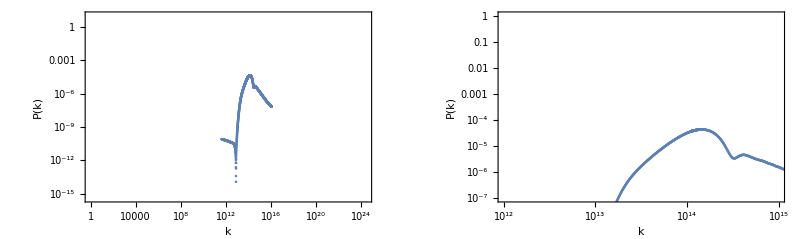

```mathematica
c=ListLogLogPlot[PPlist,Frame->True,FrameLabel->{"k","P(k)"},PlotRange->{{1,3*10^24},{4*10^-16,10}},GridLines->{{0.05},{10^-2,10^-3}}(*,Joined->True*)];

cc=ListLogLogPlot[PPlist,Frame->True,FrameLabel->{"k","P(k)"},GridLines->{{0.05},{10^-2}},PlotRange->{{10^12,10^15},{10^-7,1}}(*,Joined->True*)];

GraphicsRow[{c,cc},ImageSize->Full]
```

```mathematica
(*++++++++++++++++We create a list of the Masses+++++++++++++++++++*)
(*eg*)  MMm=M[PPlist[[55,1]]]

MassKList=Table[M[PPlist[[i,1]]],{i,1,Length[PPlist]}];
```

6.36385×10^-10

```mathematica
(*Create a list of Subscript[P, k](M)*)
PMList=Table[{M[PPlist[[i,1]]]/Mm,PPlist[[i,2]]},{i,1,Length[PPlist]}]; 

ListLogLogPlot[PMList,Frame->True,FrameLabel->{"M/M_o","P_k(M)"},GridLines->{{10^-16,10^-15,10^-13,1},{1}},Joined->True]
```

-Graphics-

The next table does the following computation: It actually does “qqq” repetitions and for each repetition the variance is calculated for different smoothing scale. The each integration runs from k_*to k_end 
σ(k) || k

σ^2=∫ dq/q e^(-(q/k)^2)16/81(q/k)^4 P(q)   Radiation Domination

σ^2=∫ dq/q e^(-(q/k)^2)4/25(q/k)^4 P(q)   Matter Domination

```mathematica
SetSystemOptions["CatchMachineUnderflow"->False];
W[x_]=Exp[-x^2/2];

 R=5*10^(13);

(*+++++++++++++++++++++ MANY POINT CALCULATION +++++++++++++++++++++++++++*)
dataaa= Table[{PPlist[[i,1]],1/PPlist[[i,1]] W[PPlist[[i,1]]/R]^2 (4/25)(PPlist[[i,1]]/R)^4 PPlist[[i,2]]},{i,1,qq}]; (*Makes a list of {k, σ^2=4/25 Int...}*)

σ2kk=Integrate[Interpolation[dataaa][x],{x,PPlist[[1,1]],PPlist[[qq,1]]}]
σ=Sqrt[σ2kk]
```

1.22091×10^-6

0.00110495

then we can choose k_limas the lowest values of scales for the MD period.

BEGINNING OF PBH ABUNDANCE CALCULATION

Now we calculate the variance square root of σ^2

for the Radiation Domination period
σ^2=∫ dq/q e^(-(q/k)^2)16/81(q/k)^4 P(q)
for the Matter Domination period
σ^2=∫ dq/q e^(-(q/k)^2)4/25(q/k)^4 P(q)

BE CAREFUL THE FOLLOWING CALCULATION TAKES ABOUT ~ 40 mins if you integrate to large scales with small steps e.g k_final~10^17

```mathematica
(*  Now we create the table sigmak=[k,σ(k)]  *)

W[x_]=Exp[-x^2/2];

sigmak=Table[{Kk (*scale "k"*),datA=Table[{PPlist[[i,1]],(*σ^2=*)1/PPlist[[i,1]] W[PPlist[[i,1]]/Kk]^2 (4/25)(PPlist[[i,1]]/Kk)^4 PPlist[[i,2]]},{i,1,qq}];

σ2K=Sqrt[Integrate[Interpolation[datA][x],{x,PPlist[[1,1]],PPlist[[qq,1]]}]]},{Kk,(*PPlist[[1,1]]*)10^12,(*PPlist[[Length[PPlist],1]]*)10^16,10^12}];//Timing
```

{214.777,Null}

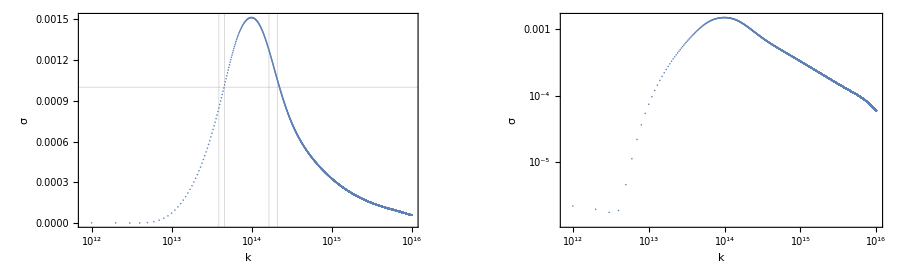

```mathematica
(*Then we plot the σ(k)*)
σk1=ListLogLinearPlot[sigmak,Frame->True,FrameLabel->{"k","σ"}(*,Joined->True*),PlotRange->All, GridLines->{ {3.9*10^13,2.1*10^14,4.6*10^13,1.65*10^14}, {0.001,0.00175,0.005}}];

σk2=ListLogLogPlot[sigmak,Frame->True,FrameLabel->{"k","σ"}(*,Joined->True*),PlotRange->All];

GraphicsRow[{σk1,σk2},ImageSize->900]
```

Now we go from σ(k) -> σ(Μ) (* We do all the calculation with k as the variable and when it comes to the abundance we map the quantities from k->M *)

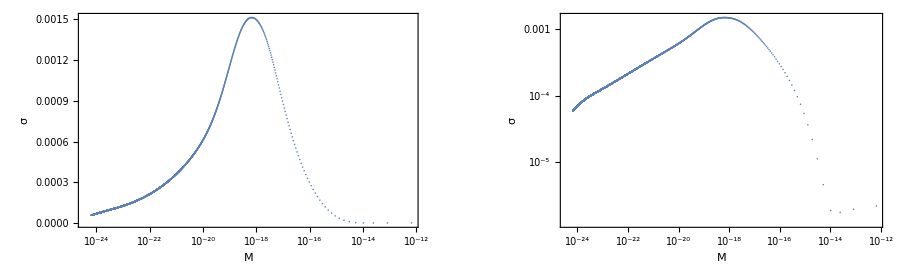

```mathematica
σm=Table[{M[sigmak[[i,1]]] (* M(k) *),sigmak[[i,2]](* σ(k) *)},{i,1,Length[sigmak]}];


(*Plots*)
σm1=ListLogLinearPlot[σm,Frame->True,FrameLabel->{"M","σ"}(*,Joined->True*),PlotRange->All];
σm2=ListLogLogPlot[σm,Frame->True,FrameLabel->{"M","σ"},(*Joined->True,*)PlotRange->All];

GraphicsRow[{σm1,σm2},ImageSize->900]
```

We assume that curvature perturbations are described by Gaussian statistics in order to estimate the PBH formation probability and connect the collapse threshold to the power spectrum:
Radiation Domination ->  β(k)=1/2 Erfc(δ_c/(√2 σ(k))),  
Matter Domination      ->  β(k) = 0.056 σ^5(k)

BE CAREFUL THE FOLLOWING CALCULATION TAKE ABOUT ~ 40 mins because it integrates the for k_final~10^17

## CALCULATION OF RATE PRODUCTION ~ β ~ WITHOUT SPIN

```mathematica
ββ=Table[{Kk,datA=Table[{PPlist[[i,1]],(*σ^2=*)1/PPlist[[i,1]] W[PPlist[[i,1]]/Kk]^2 (4/25)(PPlist[[i,1]]/Kk)^4 PPlist[[i,2]]},{i,1,qq}];

0.056*(Sqrt[Integrate[Interpolation[datA][x],{x,PPlist[[1,1]],PPlist[[qq,1]]}]])^5},{Kk,10^12,10^16,10^12}];//Timing
```

{210.058,Null}

{0.058895,Null}

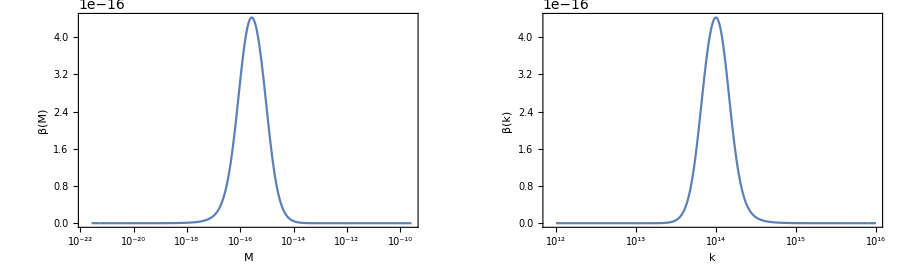

```mathematica
M[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(kreh/10^6)^-2(k/kreh)^-3;

(*Now we go from β(k)->β(Μ)*)
βm=Table[{M[ββ[[i,1]]](* M(k) *),ββ[[i,2]](*β(M)*)},{i,1,Length[ββ]}];//Timing


(*PLOT of β(M)*)
βmm=ListLogLinearPlot[βm,Frame->True,FrameLabel->{"M","β(M)"},Joined->True,PlotRange->All];
βk=ListLogLinearPlot[ββ,Frame->True,FrameLabel->{"k","β(k)"},Joined->True,PlotRange->Full];

GraphicsRow[{βmm,βk},ImageSize->900]
```

Primordial black hole as Dark Matter fraction Ω_PBH/Ω_DM. We calculate both f(M) and f(k) and compare.

WE FIND THE k_REHEATING and the corresponding Mass_REHEATING

We calculate the f (M) from the standard formula

```mathematica
fm=Table[{βm[[i,1]](*M(k)*),ⅇ^(-3/4 (4(57-Nend)-2*Log[kfinal/ββ[[i,1]]]))1.3*10^8 βm[[i,2]](γ/0.2)^(1/2)(g/106.75)^(-1/4)(βm[[i,1]]/1)^(-1/2)(*f(M)*)},{i,1,Length[βm]}];
```

```mathematica
Length[βm]
```

10000

```mathematica
3.6(γ/0.2)(g/106.75)^(-1/6)(kreh/10^6)^-2(k/kreh)^-3
```

(2.64398×10^26)/k^3

{0.053034,Null}

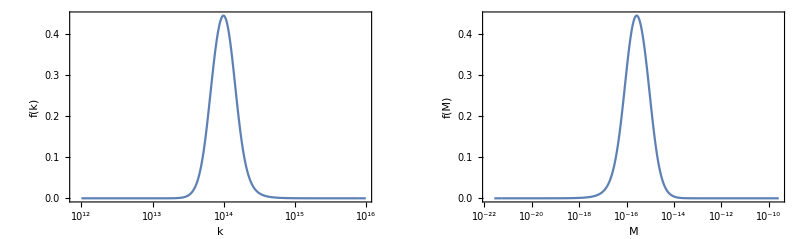

```mathematica
Kk[m_]=((2.6439838517373216*^26)/m)^(1/3); (*This is for γ=1*)

ffk=Table[{Kk[fm[[i,1]]](*k*),fm[[i,2]](*f(m)*)},{i,1,Length[fm]}];//Timing
(*we find  f(k) ->  [k,f(k)] *)

(*Plots of f(k) and f(M) for spinless black holes*)
Dfk=ListLogLinearPlot[ffk,Frame->True,FrameLabel->{"k","f(k)"},PlotRange->All,Joined->True];
Dfm=ListLogLinearPlot[fm,Frame->True,FrameLabel->{"M","f(M)"},PlotRange->All,Joined->True];

GraphicsGrid[{{Dfk,Dfm}},ImageSize->800]
```

Finally we want to calculate the integral

(f(M))_(PBH,tot)=∫ dln k  f(M)

```mathematica
(*Relation which connects PBH mass to wavenumber*)
(*1*)   Subscript[M, PBH]=M[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(kreh/10^6)^-2(k/kreh)^-3
(*test*)
M[k_]=(2.6439838517373216*^26)/k^3;

(*We make the table [M(k),1/(M(k))f(k)]*)
fMoverM=Table[{M[ββ[[i,1]]](*M(k)*),1/(M[ββ[[i,1]]](*M(k)*))fm[[i,2]](*f(k)*)},{i,1,Length[ββ]}];

(*  Subscript[f(M), PBH,tot]=∫ dln M  f(M)  *)
Integrate[Interpolation[fMoverM][x],{x,M[ββ[[Length[ββ],1]]](*Lightest Mass Subscript[M, i]*),M[ββ[[1,1]]](*Highest Mass Subscript[M, f]*)}]
```

(2.64398×10^26)/k^3

1.32628

```mathematica
M[ββ[[1,1]]]
```

1.8×10^-11

## CALCULATION OF RATE PRODUCTION ~ β ~ WITH SPIN

```mathematica
ββR=Table[{Kk,datA=Table[{PPlist[[i,1]],(*σ^2=*)1/PPlist[[i,1]] W[PPlist[[i,1]]/Kk]^2 (4/25)(PPlist[[i,1]]/Kk)^4 PPlist[[i,2]]},{i,1,qq}];

2*10^-6*Sqrt[Integrate[Interpolation[datA][x],{x,PPlist[[1,1]],PPlist[[qq,1]]}]]^2Exp[-0.147*(Sqrt[Integrate[Interpolation[datA][x],{x,PPlist[[1,1]],PPlist[[qq,1]]}]])^(-2/3)]},{Kk,10^12,10^16,10^12}];//Timing
```

{304.693,Null}

{0.065121,Null}

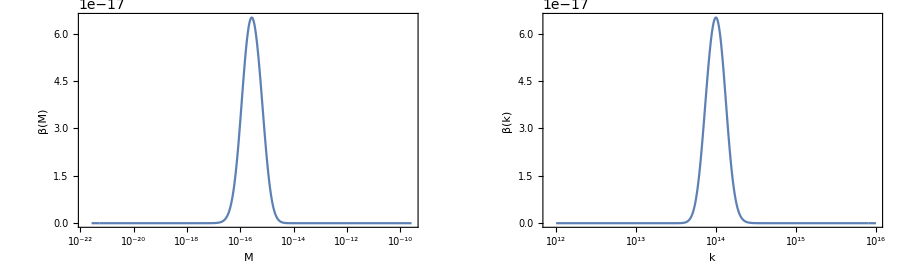

```mathematica
M[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(kreh/10^6)^-2(k/kreh)^-3;

(*Now we go from β(k)->β(Μ)*)

βmR=Table[{M[ββR[[i,1]]](* M(k) *),ββR[[i,2]](*β(M)*)},{i,1,Length[ββR]}];//Timing

(*PLOT of β(M)*)
βmmR=ListLogLinearPlot[βmR,Frame->True,FrameLabel->{"M","β(M)"},Joined->True,PlotRange->All];
(*PLOT of β(k)*)
βkR=ListLogLinearPlot[ββR,Frame->True,FrameLabel->{"k","β(k)"},Joined->True,PlotRange->Full];

GraphicsRow[{βmmR,βkR},ImageSize->900]
```

```mathematica
M[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(kreh/10^6)^-2(k/kreh)^-3
```

(2.64398×10^26)/k^3

Primordial black hole as Dark Matter fraction Ω_PBH/Ω_DM. We calculate both f(M) and f(k) and compare.

```mathematica
PPlist[[qq,1]]
```

1.22196×10^16

```mathematica
Nend=50.2(*49.05*); (*Put the number of efolds the inflation lasts for the specific model*)

kfinal=1.1841078141826195*^19;  (*Check the MD file to find it out*)

kreheating=Exp[-(2(57-Nend))]*kfinal

Mmm2[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(k/10^6)^-2/.k->kreheating
```

1.46888×10^13

8.34257×10^-14

```mathematica
(*f(m)->Table[M,f(M)]*)

fmR=Table[{βmR[[i,1]](*M(k)*),ⅇ^(-3/4 (4(57-Nend)-2*Log[kfinal/ββR[[i,1]]]))1.3*10^8 βmR[[i,2]](γ/0.2)^(1/2)(g/106.75)^(-1/4)(βmR[[i,1]]/1)^(-1/2)(*f(M)*)},{i,1,Length[βmR]}];
```

We calculate the f(k)

```mathematica
M[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(kreh/10^6)^-2(k/kreh)^-3
```

(2.64398×10^26)/k^3

{0.047779,Null}

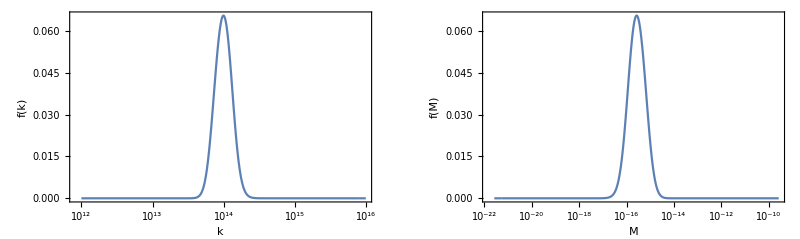

```mathematica
Kk[m_]=((2.6439838517373216*^26)/m)^(1/3); (*This is for γ=1*)

ffkR=Table[{Kk[fmR[[i,1]]](*k*),fmR[[i,2]](*f(m)*)},{i,1,Length[fmR]}];//Timing
(*we find  f(k) ->  [k,f(k)] *)

DfkR=ListLogLinearPlot[ffkR,Frame->True,FrameLabel->{"k","f(k)"},PlotRange->All,Joined->True];
DfmR=ListLogLinearPlot[fmR,Frame->True,FrameLabel->{"M","f(M)"},PlotRange->All,Joined->True];
GraphicsGrid[{{DfkR,DfmR}},ImageSize->800]
```

Finally we want to calculate the integral

(f(M))_(PBH,tot)=∫ dln k  f(M)

```mathematica
3.6(γ/0.2)(g/106.75)^(-1/6)(kreh/10^6)^-2(k/kreh)^-3
```

(2.64398×10^26)/k^3

```mathematica
(*Relation which connects PBH mass to wavenumber*)
(*1*)   Subscript[M, PBH]=M[k_]=3.6(γ/0.2)(g/106.75)^(-1/6)(kreh/10^6)^-2(k/kreh)^-3
(*test*)
M[k_]=(2.6439838517373216*^26)/k^3;

(*We make the table [M(k),1/(M(k))f(k)]*)
fMoverMR=Table[{M[ββR[[i,1]]](*M(k)*),1/(M[ββR[[i,1]]](*M(k)*))fmR[[i,2]](*f(k)*)},{i,1,Length[ββR]}];

(*  Subscript[f(M), PBH,tot]=∫ dln M  f(M)  *)
Integrate[Interpolation[fMoverMR][x],{x,M[ββR[[Length[ββR],1]]](*Highest Mass Subscript[M, f]*),M[ββR[[1,1]]](*Lightest Mass Subscript[M, i]*)}]
```

(2.64398×10^26)/k^3

0.138238

OBSERVATIONAL CONSTRAINTS

```mathematica
Femto10={{7.215694633714848*^-17,0.4225706024204134},{9.042559825430532*^-17,0.346392392409924},{1.268560715912728*^-16,0.24870439112267212},{1.992222076446007*^-16,0.1785659140299498},{2.4966116536630553*^-16,0.14637524193450863},{4.38918721965975*^-16,0.12820757007713587},{9.670088830453963*^-16,0.13699056203942026},{2.6698696975354583*^-15,0.16711736630290386},{5.882154451116472*^-15,0.2327589957925409},{8.251944367160743*^-15,0.34639239240992187},{9.237680000320667*^-15,0.4824510294242719},{1.1576470221007345*^-14,0.671951812143415},{1.2959336936453652*^-14,0.8758828910048683},{1.2959336936453652*^-14,1.}};

Femto10CUT={(*{6.715694633714848*^-17,0.4225706024204134},*){7.215694633714848*^-17,0.4225706024204134},{9.042559825430532*^-17,0.346392392409924},{1.268560715912728*^-16,0.24870439112267212},{1.992222076446007*^-16,0.1785659140299498},{2.4966116536630553*^-16,0.14637524193450863},{4.38918721965975*^-16,0.12820757007713587},{9.670088830453963*^-16,0.13699056203942026},{2.6698696975354583*^-15,0.16711736630290386},{5.882154451116472*^-15,0.2327589957925409},{6.131944367160743*^-15,0.24639239240992187},{6.541944367160743*^-15,0.2639239240992187}(*,{9.237680000320667*^-15,0.4824510294242719},{1.1576470221007345*^-14,0.671951812143415},{1.2959336936453652*^-14,0.8758828910048683},{1.2959336936453652*^-14,1.}*)};


WD10={{6.584806939333661*^-15,0.10509516438130892},{8.251944367160642*^-15,0.09205105640893374},{1.1576470221007297*^-14,0.11229481712787227},{1.624037400339145*^-14,0.14637524193450951},{2.278326145489651*^-14,0.20386962214216423},{3.196213353299468*^-14,0.30339917008610046},{4.483897013618429*^-14,0.4225706024204134},{6.290359937324404*^-14,0.628870396334644},{7.882949451737491*^-14,0.7671708387550648},{9.87874981365207*^-14,1.}};

WD10CUT={{6.584806939333661*^-15,0.10509516438130892},{8.251944367160642*^-15,0.09205105640893374},{1.1576470221007297*^-14,0.11229481712787227},{1.624037400339145*^-14,0.14637524193450951},{2.278326145489651*^-14,0.20386962214216423},{3.196213353299468*^-14,0.30339917008610046},{4.483897013618429*^-14,0.4225706024204134},{5.40359937324404*^-14,0.528870396334644},{5.60359937324404*^-14,0.5408870396334644},{5.90359937324404*^-14,0.60870396334644}(*prin htan edw*),{6.290359937324404*^-14,0.628870396334644},{8.342571137970016*^-14,0.628870396334644}(*,{7.882949451737491*^-14,0.7671708387550648},{9.87874981365207*^-14,1.}*)};

Kep10={{3.4180218482566466*^-13,0.9358861528011254},{4.2833945470856333*^-13,0.7179845648236842},{6.009079462107862*^-13,0.5155018353250516},{7.530454556376062*^-13,0.3701223609016646},{1.0564308124696155*^-12,0.26574214222349435},{1.4820434187339352*^-12,0.19079875633964766},{1.857266272767386*^-12,0.14637524193450951},{2.916759776676187*^-12,0.10509516438130956},{4.5806504536151906*^-12,0.07545670586338749},{1.0091913279368402*^-11,0.0474524885224151},{2.2234116021210858*^-11,0.03889807036015874},{3.9088857787532214*^-11,0.031885785653351754},{7.692946554041374*^-11,0.027928214120019598},{1.6948804601522992*^-10,0.026137628867391},{3.3356371952110457*^-10,0.026137628867391},{1.3669782022938304*^-9,0.04156282283238898},{3.56712132477627*^-9,0.0507032702432767},{9.30838145357531*^-9,0.057888184326909425},{2.5700038553663365*^-8,0.057888184326909425},{5.662133860384365*^-8,0.06185387416369976},{8.892146773072757*^-8,0.06185387416369976},{1.5632906669503587*^-7,0.0806259454075109},{2.455083260527815*^-7,0.10509516438131074},{4.3161779103685803*^-7,0.16711736630290694},{6.778378686209039*^-7,0.24870439112267517},{9.509237522236146*^-7,0.3701223609016669},{1.4933863775165935*^-6,0.5508168208089749},{1.8714810349761835*^-6,0.819726669166882},{2.345301468532118*^-6,1.}};


Kep10CUT={{3.4180218482566466*^-13,0.9358861528011254},{4.2833945470856333*^-13,0.7179845648236842},{6.009079462107862*^-13,0.5155018353250516},{7.530454556376062*^-13,0.3701223609016646},{1.0564308124696155*^-12,0.26574214222349435},{1.4820434187339352*^-12,0.19079875633964766},{1.857266272767386*^-12,0.14637524193450951},{2.916759776676187*^-12,0.10509516438130956},{4.5806504536151906*^-12,0.07545670586338749},{1.0091913279368402*^-11,0.0474524885224151},{2.2234116021210858*^-11,0.03889807036015874},{3.9088857787532214*^-11,0.031885785653351754},{7.692946554041374*^-11,0.027928214120019598},{1.6948804601522992*^-10,0.026137628867391},{3.3356371952110457*^-10,0.026137628867391},{1.3669782022938304*^-9,0.04156282283238898}(*,{3.56712132477627*^-9,0.0507032702432767},{9.30838145357531*^-9,0.057888184326909425},{2.5700038553663365*^-8,0.057888184326909425},{5.662133860384365*^-8,0.06185387416369976},{8.892146773072757*^-8,0.06185387416369976},{1.5632906669503587*^-7,0.0806259454075109},{2.455083260527815*^-7,0.10509516438131074},{4.3161779103685803*^-7,0.16711736630290694},{6.778378686209039*^-7,0.24870439112267517},{9.509237522236146*^-7,0.3701223609016669},{1.4933863775165935*^-6,0.5508168208089749},{1.8714810349761835*^-6,0.819726669166882},{2.345301468532118*^-6,1.}*)};


HSC10={{3.785695644098578*^-14,1.},{5.94527825296265*^-14,0.5885510958361514},{7.450500195788969*^-14,0.39547797538609625},{9.336813317322828*^-14,0.28394708205493774},{1.309840887406306*^-13,0.19079875633965115},{2.0570508764690408*^-13,0.11229481712787504},{2.885791172963822*^-13,0.07545670586338933},{3.6164140321706334*^-13,0.05788818432691043},{4.5320155438165574*^-13,0.04156282283238996},{7.117342752247852*^-13,0.026137628867391613},{9.984762712651405*^-13,0.0175632270825759},{1.5680656396416117*^-12,0.013473995652185397},{2.75674979526928*^-12,0.00905387579529851},{4.329361403424796*^-12,0.006945869487863323},{9.538282888170431*^-12,0.004987027081565644},{2.3524650438682616*^-11,0.00382590174905893},{5.182860699778358*^-11,0.0033510418846663587},{1.1418679781586332*^-10,0.0033510418846663587},{2.0074697355990864*^-10,0.0033510418846663587},{4.4227802771183914*^-10,0.003580608468921833},{1.3669782022938304*^-9,0.004987027081565674},{3.56712132477627*^-9,0.006500543072855155},{9.30838145357531*^-9,0.007421703448730786},{2.2957635290609317*^-8,0.007930134906385295},{5.057938098493036*^-8,0.007421703448730786},{7.943282347242757*^-8,0.007421703448730786},{1.3964748305774016*^-7,0.009053875795298733},{1.9590836500183497*^-7,0.01180164226522358},{2.748355117995443*^-7,0.016437181025084867},{4.831766743255008*^-7,0.022893501936384203},{6.778378686209095*^-7,0.03188578565335364},{1.0645163051151815*^-6,0.0507032702432794},{1.4933863775166058*^-6,0.07545670586339243},{1.8714810349761951*^-6,0.09835710907083131},{2.9390834721277242*^-6,0.17856591402996258},{3.683198843320025*^-6,0.2657421422235118},{5.167078185527541*^-6,0.42257060242044103},{6.475275907186635*^-6,0.5885510958361833},{7.248779691537976*^-6,0.7671708387551149},{0.00001016915268741752,1.0685060324987845}};



HSC10CUT={(*{3.785695644098578*^-14,1.},*){5.94527825296265*^-14,0.5885510958361514},{7.450500195788969*^-14,0.39547797538609625},{9.336813317322828*^-14,0.28394708205493774},{1.309840887406306*^-13,0.19079875633965115},{2.0570508764690408*^-13,0.11229481712787504},{2.885791172963822*^-13,0.07545670586338933},{3.6164140321706334*^-13,0.05788818432691043},{4.5320155438165574*^-13,0.04156282283238996},{7.117342752247852*^-13,0.026137628867391613},{9.984762712651405*^-13,0.0175632270825759},{1.5680656396416117*^-12,0.013473995652185397},{2.75674979526928*^-12,0.00905387579529851},{4.329361403424796*^-12,0.006945869487863323},{9.538282888170431*^-12,0.004987027081565644},{2.3524650438682616*^-11,0.00382590174905893},{5.182860699778358*^-11,0.0033510418846663587},{1.1418679781586332*^-10,0.0033510418846663587},{2.0074697355990864*^-10,0.0033510418846663587},{4.4227802771183914*^-10,0.003580608468921833},{1.3669782022938304*^-9,0.004987027081565674},{3.56712132477627*^-9,0.006500543072855155},{6.601200433437771*^-9,0.006500543072855155}(*,{9.30838145357531*^-9,0.007421703448730786},{2.2957635290609317*^-8,0.007930134906385295},{5.057938098493036*^-8,0.007421703448730786},{7.943282347242757*^-8,0.007421703448730786},{1.3964748305774016*^-7,0.009053875795298733},{1.9590836500183497*^-7,0.01180164226522358},{2.748355117995443*^-7,0.016437181025084867},{4.831766743255008*^-7,0.022893501936384203},{6.778378686209095*^-7,0.03188578565335364},{1.0645163051151815*^-6,0.0507032702432794},{1.4933863775166058*^-6,0.07545670586339243},{1.8714810349761951*^-6,0.09835710907083131},{2.9390834721277242*^-6,0.17856591402996258},{3.683198843320025*^-6,0.2657421422235118},{5.167078185527541*^-6,0.42257060242044103},{6.475275907186635*^-6,0.5885510958361833},{7.248779691537976*^-6,0.7671708387551149},{0.00001016915268741752,1.0685060324987845}*)};


EROS10={{4.036084637484883*^-8,1.},{5.6621338603844113*^-8,0.6288703963346929},{6.33850379910012*^-8,0.4225706024204488},{9.954357755055165*^-8,0.28394708205495806},{1.5632906669503683*^-7,0.2178359211021547},{2.1931058969265144*^-7,0.1564028290154968},{3.8556066018625575*^-7,0.13699056203943538},{6.778378686209095*^-7,0.11229481712788503},{1.334029897714027*^-6,0.1050951643813217},{2.3453014685321375*^-6,0.10509516438132235},{5.167078185527498*^-6,0.10509516438132299},{9.084021338130308*^-6,0.11229481712788732},{0.000015970233216663105,0.11998768951948734},{0.000025080589979751875,0.11998768951948807},{0.00004936026509313825,0.11229481712788904},{0.00008677819170953016,0.09835710907083986},{0.00017078523872618873,0.0861493090438496},{0.0003002502956451766,0.07061888615354289},{0.0008289780787685713,0.050703270243284686},{0.0018263726879284537,0.041562822832395915},{0.004504456363687841,0.0364041654207626},{0.007919093974429553,0.0340701543215731},{0.01953117974416327,0.0364041654207629},{0.043030345628379034,0.04156282283239664},{0.07564982836337929,0.04745248852242441},{0.13299675956203397,0.05788818432692044},{0.18657821212264303,0.05788818432692079},{0.3280152533591409,0.05070327024328681},{0.4601653432928822,0.05417675012236442},{0.6455557813221896,0.07545670586340461},{1.0138186237322362,0.11229481712789811},{1.9952623149688258,0.16711736630294383},{3.133476846886012,0.21783592110218522},{6.903555929862501,0.3241838434921761},{9.684845908457087,0.395477975386186},{15.209649474226227,0.5508168208091044},{19.060419304871775,0.717984564823859}};


CMB10={{9451.411862277744,0.00006719518121434185},{6737.1593749802,0.00011801642265222953},{4802.3847765052315,0.00021425711451386346},{3832.1606635555395,0.0003188578565335182},{3057.950588038721,0.0005417675012235306},{2179.7696230609854,0.0009835710907082538},{1739.39153021936,0.001671173663029059},{1387.9828691025853,0.0024870439112267364},{1107.569176606994,0.004225706024204134},{883.8073641089258,0.006719518121434185},{705.2520721514585,0.013034906300958566},{502.71807840509746,0.027018092005137904},{320.10909475589403,0.056001729413614164},{255.437566554716,0.10863536378740991},{203.83160452579833,0.24059963492679937},{129.7911358477477,0.49870270815654555},{103.56947816994445,0.7930134906384897},{103.56947816994445,0.9674120904770179}};

UFD10={{10580.429829653898,0.003033991700861001},{5376.053428124171,0.00515501835325051},{3423.2379342630365,0.007671708387550639},{1947.1704651060807,0.012199188310127286},{989.3825319588277,0.020727492305143345},{502.718078405083,0.03521782977176571},{255.43756655470867,0.06831756428094825},{129.79113584774402,0.11607754154954239},{73.82643894710947,0.18458102373096014},{41.993184295767115,0.2935120253819988},{21.337280812389622,0.46672895892814903},{15.209649474224921,0.6500543072855162},{10.84174872903511,0.9053875795298677}};

Radio10={{145.29532998440808,0.019398573030676033},{129.79113584774348,0.028868994294096353},{92.51777199086337,0.04590611111980882},{65.94855710481247,0.07299772955981325},{47.009478185836564,0.10863536378741546},{33.50931599295583,0.17274682417966275},{23.886124706103942,0.24059963492681166},{19.060419304869903,0.3580608468921866},{15.20964947422461,0.498702708156572},{10.841748729034888,0.7421703448730809}};

EG10={{6.675799908777158*^-19,1.785659140299602*^-7},{7.473257278474755*^-19,2.6574214222350794*^-7},{8.365974881429097*^-19,4.824510294243021*^-7},{1.173644110713773*^-18,1.3034906300959286*^-6},{1.6464793621013692*^-18,3.7630463562645612*^-6},{2.309809477233271*^-18,0.000013252632599818597},{3.2403806229963843*^-18,0.00003825901749058781},{4.5458582993033295*^-18,0.00011801642265222953},{5.696775946880334*^-18,0.0002792821412001957},{7.139082226546229*^-18,0.0005788818432690925},{8.94655073547327*^-18,0.0011998768951947125},{1.1211633025428775*^-17,0.0021783592110213466},{1.40501874759933*^-17,0.00451519237842824},{1.971069722218343*^-17,0.01000000000000001},{2.2065237648274084*^-17,0.0193985730306751},{2.765170113554801*^-17,0.0376304635626435},{3.465254206085899*^-17,0.07799851439336582},{4.342585164628078*^-17,0.13252632599817826},{4.8613284748520736*^-17,0.24059963492679937},{6.092116670171166*^-17,0.46672895892812805},{6.819850185565801*^-17,0.7421703448730415},{7.34515074422419*^-17,0.9674120904770179}};

EG10CUT={{6.675799908777158*^-19,1.785659140299602*^-7},{7.473257278474755*^-19,2.6574214222350794*^-7},{8.365974881429097*^-19,4.824510294243021*^-7},{1.173644110713773*^-18,1.3034906300959286*^-6},{1.6464793621013692*^-18,3.7630463562645612*^-6},{2.309809477233271*^-18,0.000013252632599818597},{3.2403806229963843*^-18,0.00003825901749058781},{4.5458582993033295*^-18,0.00011801642265222953},{5.696775946880334*^-18,0.0002792821412001957},{7.139082226546229*^-18,0.0005788818432690925},{8.94655073547327*^-18,0.0011998768951947125},{1.1211633025428775*^-17,0.0021783592110213466},{1.40501874759933*^-17,0.00451519237842824},{1.971069722218343*^-17,0.01000000000000001},{2.2065237648274084*^-17,0.0193985730306751},{2.765170113554801*^-17,0.0376304635626435},{3.465254206085899*^-17,0.07799851439336582},{4.342585164628078*^-17,0.13252632599817826},{4.8613284748520736*^-17,0.24059963492679937},{6.092116670171166*^-17,0.46672895892812805},{6.819850185565801*^-17,0.7421703448730415},{7.184515074422419*^-17,0.9074120904770179}};

REH={{8.342571137970016*^-14,1.2*10^-5},{8.342571137970016*^-14,10^-6},{8.342571137970016*^-14,10^-7},{8.342571137970016*^-14,10^-8},{8.342571137970016*^-14,10^-9},{8.342571137970016*^-14,10^-10},{8.342571137970016*^-14,10^-12},{8.342571137970016*^-14,10^-13}};


Ticks2={{{{10^-9,  Superscript[10,-9]},{10^-8,  Superscript[10,-8]},{10^-7,  Superscript[10,-7]},{10^-6, Superscript[10,-6]},{10^-5,Superscript[10,-5] },{10^-4, Superscript[10,-4]},{10^-3,Superscript[10,-3]},{10^-2, Superscript[10,-2]},{10^-1, Superscript[10,-1]},{0, 1},{10^0, Superscript[1,""]}}, None},  {{{10^-18, "",0.01 },{10^-17, "",0.01 },{10^-16, "",0.01 },{10^-15, Superscript[10,-15]},{10^-14, "",0.01 },{10^-13, "",0.01 },{10^-12, "",0.01 },{10^-11, "",0.01 },{10^-10, Superscript[10,-10]},{10^-9, "",0.01 },{10^-8, "",0.01 },{10^-7, "",0.01 },{10^-6, "",0.01 },{10^-5, Superscript[10,-5]},{10^-4, "",0.01 },{10^-3, "",0.01 },{10^-2, "",0.01 },{10^-1, "",0.01 },{10^0, Superscript[10,0]},{10^1, "",0.01 },{10^2, "",0.01 },{10^3, "",0.01 },{10^4, Superscript[10,4]}}, { {10^-17.3,  Superscript[10,16]},{10^-16.3,"",0.01},{10^-15.3,  "",0.01},{10^-14.3,  "",0.01},{10^-13.3,"",0.01},{10^-12.3 ,Superscript[10,21]} ,{10^-11.3,  "",0.01},{10^-10.3, "",0.01},{10^-9.3,"",0.01},{10^-8.3,  "",0.01}, {10^-7.3,Superscript[10,26]},{10^-6.3,"",0.01},{10^-5.3,"",0.01},{10^-4.3, "",0.01}, {10^-3.3, "",0.01},{10^-2.3, Superscript[10,31]}, {10^-1.3, "",0.01},{10^-0.3, "",0.01},{10^0.7, "",0.01},{10^1.7, "",0.01},{10^2.7,Superscript[10,36]},{10^3.7, "",0.01}}}};


ticksA={{     {{10^-9, "",0.01 },{10^-8,Superscript[10,-8]},{10^-7, "",0.01 }, {10^-6, Superscript[10,-6]},{10^-5, "",0.01 },{10^-4, Superscript[10,-4]}, {10^-3, "",0.01 },{10^-2, Superscript[10,-2]}, {10^-1, "",0.01 },{0,1}}, None},  {{ {10^-19," ", 0.01},{-18," ", 0.01} , {10^-17, Superscript[10,-17]},{10^-16," ", 0.01}, {10^-15, Superscript[10,-15]},{-14," ", 0.01}, {10^-13," ", 0.01}, {-12," ", 0.01}, {10^-11," ", 0.01},  {-10, Superscript[10,-10]},{10^-9," ", 0.01},{-8," ", 0.01} , {10^-7," ", 0.01}, {10^-6," ", 0.01} , {10^-5, Superscript[10,-5]},{-4," ", 0.01}, {10^-3," ", 0.01}, {10^-2," ", 0.01}, {10^-1," ", 0.01},{0, 1}, {1," ", 0.01},  {2," ", 0.01}, {3," ", 0.01},{4, Superscript[10,4]}}, {{10^-15.3," ", 0.01}, {10^-17.3,  Superscript[10,16]},{-16.3," ", 0.01},{10^-15.3," ", 0.01},{10^-14.3," ", 0.01}, {10^-13.3," ", 0.01},{-12.3 ,Superscript[10,21]} , 
{10^-11.3," ",0.01},{10^-10.3," ", 0.01},{-9.3," ", 0.01}, {-8.3," ", 0.01},{10^-7.3,Superscript[10,26]},{-6.3," ", 0.01},{-5.3," ", 0.01},{-4.3," ", 0.01}, {10^-3.3," ", 0.01}, {-2.3, Superscript[10,31]}, {-1.3," ", 0.01},{-0.3," ", 0.01},{1.3," ", 0.01}, {2.3," ", 0.01},{3.3, Superscript[10,36]}}}} ;


APlot=Show[ ListLogLogPlot[{Kep10, EROS10, EG10, Femto10, WD10, HSC10, CMB10, UFD10, Radio10}, Filling->{1->{
Top,1->Bottom}, 2->{Top,Bottom}, 3->Top, 4->Top, 5->Top, 7->Top, 8->Top, 9->Top}, PlotStyle->{{Thick, Blue},{Thick, Blue},{Thick, Green},{Thick, Blue},{Thick, Orange},{Dashed, Thick, Blue}, {Red, Thick}, {Thick, Orange},{Thick, Dashed, Orange}, {Thick, Dashed, Black}}, PlotRange->{{10^-18.2,10^4},{10^-7,1}}, PlotRangePadding->.01, Frame->True, 
FrameStyle->{20,20},  
FrameTicks->Ticks2,
FrameLabel->{{"Ω_PBH/Ω_cr", " "},{"M_PBH/M_⊙", "M_PBH[g]" }}, 
 Axes->False,Joined->True],ImageSize->500];
```

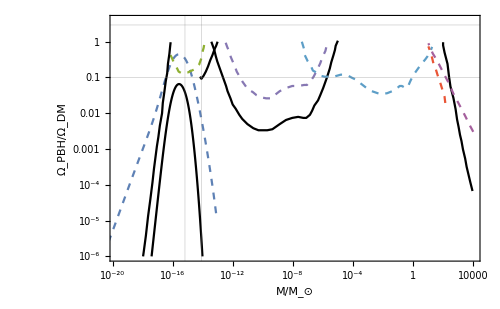

```mathematica
PBH=ListLogLogPlot[{fm,fmR,Femto10,WD10,Kep10,HSC10,EROS10,CMB10,UFD10,EG10,Radio10},


Frame->True,FrameLabel->{"M/M_⊙","Ω_PBH/Ω_DM"},PlotRange->{{2*10^-20,10^4},{10^-6,4}},BaseStyle->{FontFamily->"Arial",20},GridLines->{{8.506616257088846*^-15, 6.611570247933884*^-16},{0.1,2.94}},PlotStyle->{Dashed,Black},Joined->True,ImageSize->500]
```

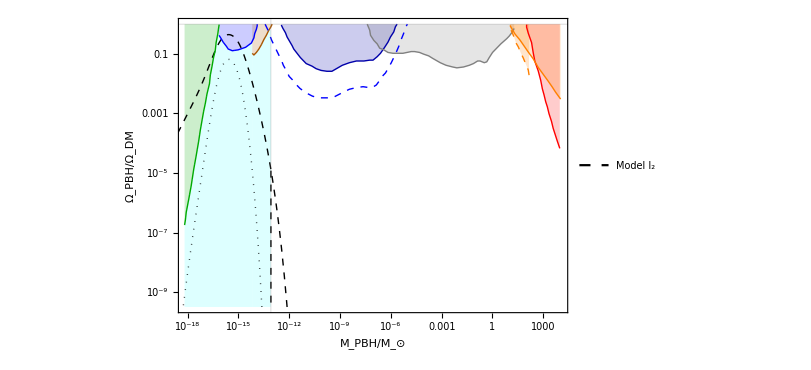

```mathematica
PBH2=ListLogLogPlot[{fm,Kep10, EROS10, EG10,Femto10, WD10,HSC10, CMB10, UFD10, Radio10,EG10CUT,Femto10CUT,WD10CUT(*,HSC10CUT*),REH,fmR},Filling->{ 2->Top,3->Top, 4->Top, 5->Top, 6->Top, 8->Top, 9->Top, 10->Top,11->Bottom,12->Bottom,13->Bottom,14->Bottom},PlotStyle->{ {Thick, Dashed, Black},{Thick, Darker[Blue]},{Thick, Gray},{Thick,Darker[Green]},{Thick,Blue},{Thick, Darker[Orange]},{Dashed, Thick,Blue}, {Red, Thick}, {Thick, Orange},{Thick, Dashed, Orange},{ Dotted, Thickness[0],Lighter[Cyan]},{ Dotted, Thickness[0],Lighter[Cyan]},{ Dotted, Thickness[0],Lighter[Cyan]},{Thick, Dashed, Black},{Thick, Dotted, Black}},Frame->True,FrameLabel->{{"Ω_PBH/Ω_DM", " "},{"M_PBH/M_⊙", "M_PBH[g]" }},PlotRange->{{8*10^-19,10^4},{10^-9.5,1}},BaseStyle->{FontFamily->"Arial",20},GridLines->{{8.342571137970016*^-14},{1}},PlotStyle->{Dashed,Black},Joined->True,ImageSize->600,FrameTicks->Ticks2,FrameStyle->Directive[FontSize->16],PlotLegends->Placed[LineLegend[{"Model I_2"},LabelStyle->{GrayLevel[0.1],16},LegendLayout->{"Row",1},LegendMarkerSize->15 ],{0.85,.15}]]
```